# Supporting Information for Harnessing Matrix Completion to Unify and Extend Viral Serology Studies

The following code reproduces the plots in the main text. Made on Mathematica version 13.0.0 for Windows. Sections can be opened by mouse click.

Raw data can be found here.

## Figures

### Accessing the Data

#### Influenza (Fonville 2014)

The Fonville datasets are referred to by their SI table numbering: Table S1 (Fonville Study 1), Table S3 (Fonville Study 2), Table S5 (Fonville Study 3), Table S6 (Fonville Study 4), Table S13 (Fonville Study 5), and Table S14 (Fonville Study 6). For convenience, these table indices are stored in the variable:

```mathematica
(* List of all Fonville tables *)
fonvilleTables
```

{S1,S3,S5,S6,S13,S14}

For each dataset, the variables viruses and sera contain all the viruses and sera in that study. For example, here are the viruses and sera in Table S1

```mathematica
viruses["S1"]//Short
sera["S1"]//Short
```

{NL/179/93,A/WELLINGTON/1/94,«70»,VN021/EL444/2010,VN053/2010}

{Serum_A/WELLINGTON/25/93_TableS1,«33»,Serum_A/HONGKONG/34/90_TableS1}

For convenience, the table index All can be used to get a list of the viruses or sera in all Fonville studies

```mathematica
viruses[All]//Short
sera[All]//Short
```

{A/AUCKLAND/20/2003,A/AUCKLAND/5/96,«77»,VN021/EL444/2010,VN053/2010}

{Serum_A/WELLINGTON/25/93_TableS1,«1145»,SubjectB039_TableS14_Post}

For each Fonville dataset, there are three types of data associated with it:

data: The raw data, with missing values represented by Missing[]

dataComplete: Intra-completed data, so that each virus-serum combination in that table has a value

dataAllComplete: Inter-completed data, where all six Fonville dataset were combined before completion

For example, the code below shows the raw measurements from Table S1 as well as the intra-completed measurements. Notice that the first output has Missing[] values while the second output does not.

```mathematica
(* Raw data *)
Table[data[{virus,serum}],{serum,sera["S1"]},{virus,viruses["S1"]}]
(* Intra-completed data *)
Table[dataComplete[{virus,serum}],{serum,sera["S1"]},{virus,viruses["S1"]}]
```

The intra-completed data (dataComplete) will not have virus-serum interactions if either the virus or serum do not exist in Table S1. However, the inter-completed data (dataAllComplete) will have these interactions. 
Note: It is difficult to estimate the uncertainty of these inter-table completion results. Based on the Figure 4B and Figure S5, such completions can have an RMSE anywhere from 0.2 to 1.2 for the log_10 titers.

```mathematica
(* Intra-completed data does not include viruses or sera outside of a table *)
dataComplete[{First@Complement[viruses[All],viruses["S1"]],First@sera["S1"]}]
(* Inter-completed data predicts all virus-serum interactions *)
dataAllComplete[{First@Complement[viruses[All],viruses["S1"]],First@sera["S1"]}]
```

dataComplete[{BI/16190/68,Serum_A/WELLINGTON/25/93_TableS1}]

16.5

#### HIV-1 (Catnap)

The HIV-1 data is accessible in a similar fashion to the influenza data, except that the table indices are either "CatnapMonoclonal" (for the monoclonal antibody data) or "CatnapPolyclonal" (for the polyclonal serum data)

```mathematica
(* Monoclonal antibody data *)
viruses["CatnapMonoclonal"]//Short
sera["CatnapMonoclonal"]//Short
```

{190049,191647,191859,191882,«925»,ZM53_12,ZM53_21,ZM55_28A,ZM55_4A}

{1357,1361,2158,2191,2219,«363»,VRC-PG05,VRC-PG19,VRC-PG20,Y498,Z13e1}

```mathematica
(* Polyclonal serum data *)
viruses["CatnapPolyclonal"]//Short
sera["CatnapPolyclonal"]//Short
```

{001428_2_42,00836_2_5,16055_2_3,«65»,ZM233_6,ZM249_1,ZM53_12}

{Polyclonal AIIMS_329 102-months,«38»,polyclonal QA013}

For each dataset, there are two types of data associated with it:

data: The raw data, with missing values represented by Missing[]

dataComplete: The matrix-completed dataset, where each virus-serum combination has a value

Because these two dataset have different units, we did not combine them and create a dataAllComplete variable for Catnap

For example, the code below provides the raw measurements for the monoclonal antibody dataset as well as the matrix-completed data.

```mathematica
(* Raw data *)
Table[data[{virus,serum}],{serum,sera["CatnapMonoclonal"]},{virus,viruses["CatnapMonoclonal"]}]
(* Intra-completed data *)
Table[dataComplete[{virus,serum}],{serum,sera["CatnapMonoclonal"]},{virus,viruses["CatnapMonoclonal"]}]
```

### Methods of Matrix Completion

In this manuscript, we performed matrix completion using nuclear norm minimization. This method is implemented via the function nuclearNormMinimization. Given a matrix M with missing values (denoted by the Head Missing), this method searches for a complete matrix M̃ found by the optimization algorithm

minimize | (‖M̃‖)_*
subject to | ((M̃)_measured)_(j,k)=(M_measured)_(j,k)

M_measured represents the non-missing values in M, so that M̃ must exactly match M at these measured values, and the missing values are filled in by minimizing the nuclear norm of the resulting matrix. The nuclear norm (or trace norm) is equal to (‖M̃‖)_*=Tr[((M̃)^*M̃)^(1/2)] where (M̃)^* denotes the conjugate transpose of M̃.

In this notebook, we use a related algorithm called robust PCA that scales better for larger matrices. This method is implemented with the function RPCA and solves the same minimization problem. The differences between both algorithms tend to be very minor - for example, the section below shows that for a Fonville dataset, both approaches yield the same result, although robust PCA is significantly faster for larger datasets.

Note that for both nuclear norm minimization and robust PCA, we force an exact match for the measured values in the completed matrix, whereas in our manuscript we enabled the measured values to deviated with a quadratic penalty. As shown in Table S1, the RMSE of the measured values was ≤0.06 for the log_10 data across all matrices (corresponding to 10^0.06=1.15-fold error), so that enforcing this exact match will minimally alter the results.

#### Basic Examples of Matrix Completion

Consider the following complete rank 1 matrix.

```mathematica
matrixComplete=# Range@5&/@ Range@5;
Echo[matrixComplete//MatrixForm,"Complete matrix: "];
```

Complete matrix:   (1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25)

Remove 4 entries and matrix complete using the nuclear norm and robust PCA algorithms. In this example, nuclear norm minimization leads to nearly perfect completion, while robust PCA has slightly larger error.

```mathematica
matrixIncomplete=matrixComplete;
(matrixIncomplete[[Sequence@@#]]=Missing[])&/@{{1,2},{3,4},{5,1},{2,4}};
Echo[(matrixIncomplete//MatrixForm)->(Round[nuclearNormMinimization[matrixIncomplete],0.01]//MatrixForm),"Nuclear norm matrix completion:"];
Echo[(matrixIncomplete//MatrixForm)->(Round[RPCA[matrixIncomplete],0.01]//MatrixForm),"Robust PCA matrix completion:"];
```

Nuclear norm matrix completion:  (1 | Missing[] | 3 | 4 | 5
2 | 4 | 6 | Missing[] | 10
3 | 6 | 9 | Missing[] | 15
4 | 8 | 12 | 16 | 20
Missing[] | 10 | 15 | 20 | 25)→(1. | 2. | 3. | 4. | 5.
2. | 4. | 6. | 7.99 | 10.
3. | 6. | 9. | 12. | 15.
4. | 8. | 12. | 16. | 20.
5. | 10. | 15. | 20. | 25.)

Robust PCA matrix completion:  (1 | Missing[] | 3 | 4 | 5
2 | 4 | 6 | Missing[] | 10
3 | 6 | 9 | Missing[] | 15
4 | 8 | 12 | 16 | 20
Missing[] | 10 | 15 | 20 | 25)→(1. | 2.36 | 3. | 4. | 5.
2. | 4. | 6. | 7.61 | 10.
3. | 6. | 9. | 11.44 | 15.
4. | 8. | 12. | 16. | 20.
4.32 | 10. | 15. | 20. | 25.)

Both matrix completion algorithms perform nearly identically on the datasets considered in this study. For example, when removing 50% of the data in Fonville 2014 Study 1 (Table S1) and performing matrix completion, the predictions for all 50% of values are shown below - nearly every large blue point (nuclear norm minimization) has a small gold point (robust PCA) that lies directly on top, and the RMSE of these predictions are the same up to the hundredths decimal point.

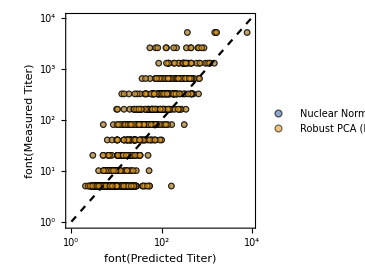

```mathematica
posWithheld=;
(* Fonville Study 1 with 50% of values withheld *)
matrixComplete=Table[data[{virus,serum}],{serum,sera["S1"]},{virus,viruses["S1"]}]/.Missing[]->Missing["Not Measured"];
matrixIncomplete=ReplacePart[matrixComplete,posWithheld->Missing["Withheld"]];
(* Matrix complete - The LogData option performs completion on the Subscript[Log, 10] titers *)
resRPCA=RPCA[matrixIncomplete,"LogData"->True];
plotDataRPCA=Transpose[Extract[#,posWithheld]&/@{resRPCA,matrixComplete}];
resNucNorm=nuclearNormMinimization[matrixIncomplete,"LogData"->True];
plotDataNucNorm=Transpose[Extract[#,posWithheld]&/@{resRPCA,matrixComplete}];
(* Plotting *)
Show[ListPlot[{plotDataRPCA,plotDataNucNorm},],Plot[{x},{x,1,10^4},PlotStyle->{Black,Thick,Dashed},ScalingFunctions->{"Log","Log"}]]
```

The primary advantage of robust PCA is that it scales better with the size of the matrix. For example, for Fonville Study 3 (Table S5), robust PCA is 10-fold faster than nuclear norm minimization

```mathematica
matrixIncomplete=Table[data[{virus,serum}],{serum,sera["S5"]},{virus,viruses["S5"]}];
Echo[First@Timing@RPCA[matrixIncomplete,"LogData"->True],"Timing for Robust PCA (seconds):"];
Echo[First@Timing@nuclearNormMinimization[matrixIncomplete,"LogData"->True],"Timing for Robust PCA (seconds):"];
```

Timing for Robust PCA (seconds):  1.8125

Timing for Robust PCA (seconds):  17.0625

### Figure 2: Influenza Intra-Table Completion (Fonville 2014)

Analysis of the influenza data in Fonville 2014. Panel A shows the intra-table completion process, where missing and withheld entries are filled in via matrix completion. Panel B shows the accuracy of imputing the withheld values. Panel C shows the approximate rank of the resulting complete matrix. All three panels correspond to a single matrix completion run for Fonville Table S1 with 50% of data observed.

In Panel D, we vary the fraction of data observed across all Fonville tables and analyze how the r^2 and the RMSE improve as more values are seen. For reference, the error of the experimental assay is approximately 2-fold, corresponding to Log_10[2]≈0.3 on the RMSE plot.

#### Panels A-C: 1 Run at 50% Observed Fraction

```mathematica
(* Fonville Study 1 with 50% of values withheld *)
posWithheld=;
dataMeasurements=Table[data[{virus,serum}],{serum,sera["S1"]},{virus,viruses["S1"]}]/.Missing[]->Missing["Not Measured"];
dataPreCompletion=ReplacePart[dataMeasurements,posWithheld->Missing["Withheld"]];
(* Matrix complete - The option specifies that the Log10[titers] are completed *)
dataPostCompletion=RPCA[dataPreCompletion,"LogData"->True];
```

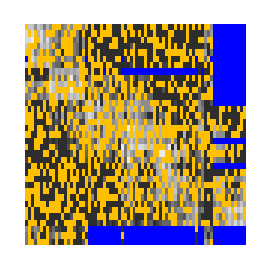
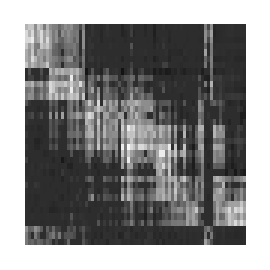
-Graphics- | -Graphics-
 |

```mathematica
(* Panel A *)
leg1=SwatchLegend[{colorMissing,colorWithheld},font/@{"Missing","Validation"},LegendFunction->"Frame"];
leg2=BarLegend[{GrayLevel,{0,4}},LegendLayout->"Row",LegendLabel->font["Titer",14],Ticks->Table[{j,Superscript[10,j]},{j,0,4}]];
{plotArrayPreCompletion,plotArrayPostCompletion}=ArrayPlot[N@#/.val_Real:>Log10@val,PlotRangePadding->None,ColorFunction->(Which[MatchQ[#,_Real],GrayLevel[Rescale[#,{0,4}]],MemberQ[#,Missing["Withheld"],All],colorWithheld,MemberQ[#,Missing["Not Measured"],All],colorMissing]&),ColorFunctionScaling->False,AspectRatio->1,ImageSize->270]&/@{dataPreCompletion,dataPostCompletion};
Grid[{{plotArrayPreCompletion,plotArrayPostCompletion},{leg1,leg2}},Spacings->{3,1}]
```

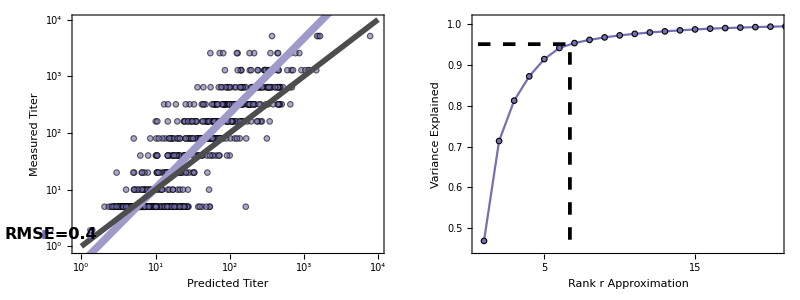

```mathematica
(* Panel B *)
plotData=Transpose[Extract[#,posWithheld]&/@{dataPostCompletion,dataMeasurements}];
fit=fitPerp[Log10@plotData];
fit=10^(fit/.x->Log10[x]);
plotScatter=Show[ListPlot[plotData,],Plot[{fit,x},{x,1,10^4},]];
(* Panel C *)
σVals=SingularValueList[Log10@dataPostCompletion-Mean@Flatten@Log10@dataPostCompletion];
plotData=Transpose[{Range@Length@σVals,Accumulate[σVals^2]/Total[σVals^2]}];
f=Interpolation[plotData];
root=x/.FindRoot[f[x]==0.95,{x,7.}];
plotRank=ListPlot[plotData,];
Grid[{{plotScatter,plotRank}},Spacings->3]
```

#### Panel D: r^2 and RMSE at Different Observed Fractions

```mathematica
(* Fraction of values measured *)
fracMeasured=Table[N@Length@DeleteMissing[Join@@Table[data[{virus,serum}],{serum,sera[table]},{virus,viruses[table]}]]/Times@@(Length/@{sera[table],viruses[table]}),{table,fonvilleTables}];
Echo[Round[100fracMeasured,0.1],"Percent of values measured in the Fonville studies:"];
(* For aesthetic purposes only, nudging the value for Study 6 so that it will not be hidden by Study 5 *)
fracMeasured[[-1]]-=0.002;
```

Percent of values measured in the Fonville studies:  {86.8,62.8,92.9,91.5,99.6,98.9}

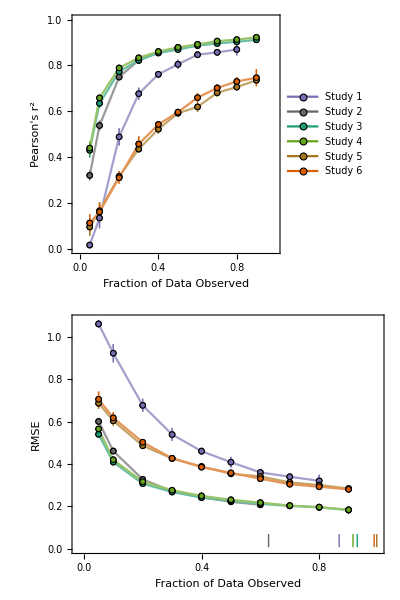

```mathematica
(* Panel D *)
leg=PointLegend[colors,font["Study "<>ToString@#]&/@Range@6,];
plots=(
plotData=Table[Cases[resIntraFonville,{table,__}][[All,#[[1]]]],{table,fonvilleTables}];
(* Plot the connecting lines slightly lighter than the PlotMarkers *)
Show[ListPlot[plotData,],ListPlot[plotData,]]
)&/@{{{2,3},"Pearson's r^2",{0,1.}},{{2,4},"RMSE",{0,1.08}}};
Grid[{{plots[[1]]},{plots[[2]]}},Spacings->2]
```

#### Inset: Bar Chart of Measured/Missing Data

```mathematica
numAccurateCompletion={0.67,0.37,0.4,0.4,0.55,0.55};
numMeasured=N@Table[Length@DeleteMissing[Join@@Table[data[{virus,serum}],{virus,viruses[table]},{serum,sera[table]}]]/Times@@(Length/@{sera[table],viruses[table]}),{table,fonvilleTables}];
numMissing=1-numMeasured;
```

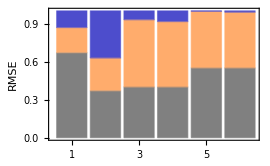

```mathematica
plot=BarChart[Transpose@{numAccurateCompletion,numMeasured-numAccurateCompletion,numMissing},]
```

### Figure 3: HIV-1 Intra-Table Completion (Catnap)

Analysis of the HIV-1 data from Catnap (a collection of multiple large-scale serological studies).The format of this figure parallels that of Figure 2.

#### Panels A-C: 1 Run at 50% Observed Fraction

For numerical stability, we always set the strongest antibody-virus interactions as the largest values. Therefore, we set up the matrix completion for the Catnap monoclonal antibody data using -Log_10[IC_50 values]. (In contrast, the polyclonal serum data and the Fonville serum data are all matrix completed as -Log_10[titers].)

```mathematica
(* Catnap monoclonal antibody data with 13% of values withheld *)
posWithheld=;
dataMeasurements=Table[data[{virus,serum}],{serum,sera["CatnapMonoclonal"]},{virus,viruses["CatnapMonoclonal"]}]/.Missing[]->Missing["Not Measured"];
dataPreCompletion=ReplacePart[dataMeasurements,posWithheld->Missing["Withheld"]];
(* Matrix complete - The option specifies that the -Log10[titers] are completed *)
(* This completion takes a while because the Catnap dataset is significantly larger than the Fonville datasets *)
dataPostCompletion=RPCA[dataPreCompletion,1000,"LogData"->True,"InvertData"->True];
```

```mathematica
(* Panel A *)
range={-5.2,4.1};
(* For better visibility, show each withheld value as a 2x6 gold square *)
posWithheldExtra=DeleteCases[Flatten[Table[pos+{x,y},{pos,posWithheld},{x,-1,1},{y,-3,3}],2],{0|(1+First@Dimensions@dataPreCompletion),_}|{_,0|(1+Last@Dimensions@dataPreCompletion)}];
(* Pre- and post-completion matrix *)
{plotArrayPreCompletion,plotArrayPostCompletion}=ArrayPlot[N@#/.val_Real:>Log10@val,PlotRangePadding->None,ColorFunction->(Which[MatchQ[#,_Real],GrayLevel[1-Rescale[#,range]],MemberQ[#,Missing["Withheld"],All],colorWithheld,MemberQ[#,Missing["Not Measured"],All],colorMissing]&),ColorFunctionScaling->False,AspectRatio->1,ImageSize->270]&/@{ReplacePart[dataPreCompletion,posWithheldExtra->Missing["Withheld"]],dataPostCompletion};
(* Plotting *)
leg1=SwatchLegend[{colorMissing,colorWithheld},font/@{"Missing","Validation"},LegendFunction->frame];
leg2=BarLegend[{GrayLevel[1-Rescale[#,range]]&,range},LegendLayout->"Row",LegendLabel->font["IC_50 (μg/mL)",14],Ticks->Table[{j,Superscript[10,j]},{j,-4,4,2}]];
Grid[{{plotArrayPreCompletion,plotArrayPostCompletion},{leg1,leg2}},Spacings->{3,1}]
```

-Graphics-

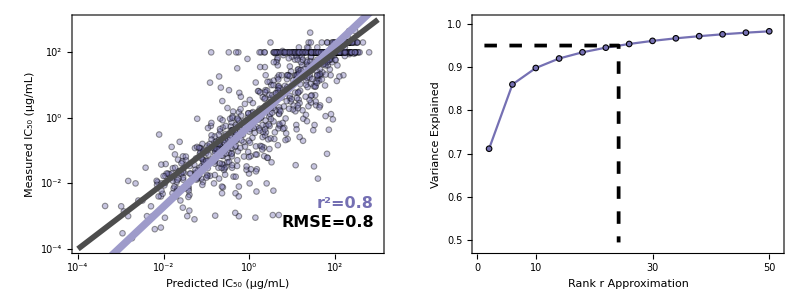

```mathematica
(* Panel B *)
plotData=Transpose[Extract[#,posWithheld]&/@{dataPostCompletion,dataMeasurements}];
fit=fitPerp[Log10@N@plotData];
fit=10^(fit/.x->Log10[x]);
plotScatter=Show[ListPlot[plotData,],Plot[{fit,x},{x,10^-4,10^3},]];
(* Panel C *)
σVals=SingularValueList[Log10@dataPostCompletion-Mean@Flatten@Log10@dataPostCompletion];
plotData=Transpose[{Range@Length@σVals,Accumulate[σVals^2]/Total[σVals^2]}][[2;;50;;4]];
f=Interpolation[plotData];
root=x/.FindRoot[f[x]==0.95,{x,7.}];
plotRank=ListPlot[plotData,];
Grid[{{plotScatter,plotRank}},Spacings->3]
```

#### Panel D: r^2 and RMSE at Different Observed Fractions

```mathematica
(* Fraction of values measured *)
fracMeasured=N@Length@DeleteMissing[Join@@Table[data[{virus,serum}],{serum,sera["CatnapMonoclonal"]},{virus,viruses["CatnapMonoclonal"]}]]/Times@@(Length/@{sera["CatnapMonoclonal"],viruses["CatnapMonoclonal"]});
Echo[ToString@Round[100fracMeasured,0.1]<>"%","Fraction of measured values:"];
```

Fraction of measured values:  13.3%

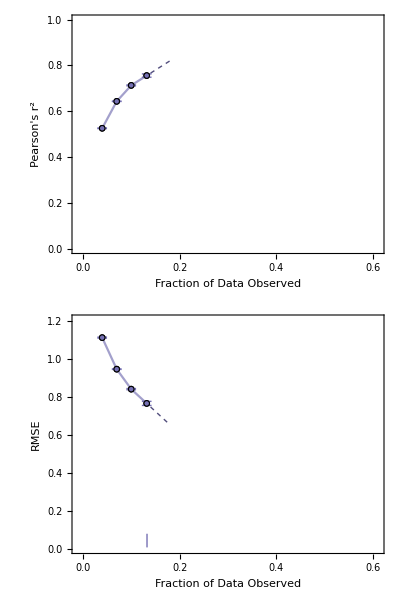

```mathematica
(* Panel D *)
plots=(
plotData=resIntraCatnap[[All,#[[1]]]];
fit=Fit[{#[[1]],#[[2]]["Value"]}&/@plotData[[-2;;]],{1,x},x];
Show[ListPlot[plotData,],ListPlot[plotData,],Plot[fit,{x,0.14,0.18},]]
)&/@{{{2,3},"Pearson's r^2",{0,1}},{{2,4},"RMSE",{0,1.21}}};
Grid[{{plots[[1]]},{plots[[2]]}},Spacings->2]
```

### Figure 4: Inter-Table Completion

Panel B examines how well a virus can be inter-table completed between two Fonville tables. For example, suppose a virus V is present in Tables S1, S5, and S6. We perform three different matrix completions, withholding all virus V data from one of the tables, performing matrix completion, and comparing the imputed values to the measured values.

Panel C demonstrates inter-table completion across the Catnap monoclonal antibody IC_50 data and the polyclonal serum ID_50 data. Although straightforward matrix completion between the two datasets leads to large error (6–10-fold), the results nevertheless allow us to accurately characterize which of the missing antibodies/sera have the strongest interactions with a virus. Said another way, given that the monoclonal antibody data spans 6 orders of magnitude, 10-fold error is more than sufficient to differentiate between the strongest and weakest interactions.

#### Panel B: Completion across Fonville Studies

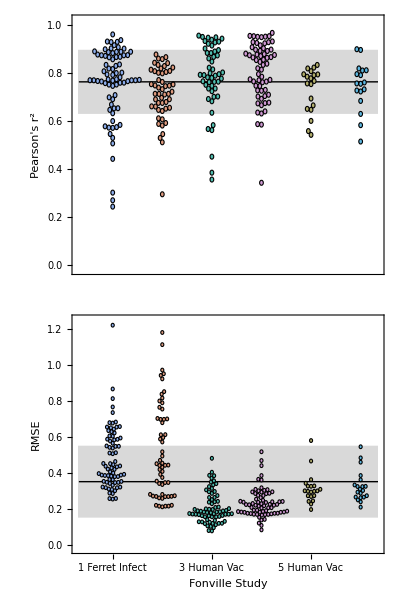

```mathematica
(* Swarm plots *)
{plotRSquared,plotRMSE}=With[{r=0.0109,type=#,offset=0.018},
plotRange={{0.3,6.35},{-0.02,If[type==="Pearson's r^2",1.02,1.25]}};
(* Compute r^2 and RMSE for all viruses in each study. For the r^2 analysis, do not consider points where the measured or predicted values have a low standard deviation (<0.2) which artifically inflates the correlation coefficient *)
pnts=Cases[resInterFonville,{_,#,__,If[type==="Pearson's r^2",(* Remove cases with artifically deflated r^2 *)False,_]}][[All,If[type==="Pearson's r^2",3,4]]]&/@fonvilleTables;
{mean,standardDeviation}={Mean[#],StandardDeviation[#]}&[Join@@pnts];
swarmPlot[pnts,r,]
]&/@{"Pearson's r^2","RMSE"};
Grid[{{plotRSquared},{plotRMSE}}]
```

#### Panel C: Completion between Catnap Monoclonal and Polyclonal Data

```mathematica
(* Analyze all viruses within either the 'withheldData'="Monoclonal" or 'withheldData'="Polyclonal" datasets *)
plotCatnapInter[withheldData_]:=Block[{x,Δx=5,threshold=80,individualResponses,meanResponse,meanResponseAvg,f,root},
(* Responses of the individual viruses *)
individualResponses=100DeleteMissing[FirstCase[resInterCatnap,{#,withheldData,__,sortedPredictions_}:>sortedPredictions]&/@viruses["CatnapPolyclonal"]];
(* Mean response across all viruses, using a window of Δx *)
meanResponse=Join@@individualResponses;
meanResponseAvg=Table[{Mean[First/@#],Around[Mean[Last/@#],StandardDeviation[Last/@#]]}&@Cases[meanResponse,{x_,_}/;xMin≤x<xMin+Δx],{xMin,0,100-Δx,Δx}];
(* Demark when 80% of the key interactions are found *)
f=Interpolation[meanResponseAvg/.Around[mean_,_]:>mean];
root=x/.FindRoot[f[x]-threshold,{x,30}];
Show[ListPlot[individualResponses,],ListPlot[meanResponseAvg,]]
]
Grid[{{plotCatnapInter["Monoclonal"]},{plotCatnapInter["Polyclonal"]}},Spacings->3]
```

-Graphics-

### Figure 5: Prioritizing Monoclonal Antibody Measurements

Using existing Catnap measurements up to a certain year to predict future measurements. In the plot below, we use predict all virus-antibody IC_50 values from 2018 and later. We sort the imputed IC_50 values from strongest-to-weakest and examined how many strong interactions (IC_50<0.1 μg/mL) are identified by N experiments (x-axis). In Figure S7, we show how potent or weak interactions could be predicted across several years.

```mathematica
predictFutureExperiments[2018,"PotentInteractions"]
```

-Graphics-

### Figure 6: Vinh Inter-Table Completion

Can the measurements from the Fonville study predict the behavior of these same viruses in the 2021 Vinh study? This study measured HAI of six H3N2 viruses against 24,000 sera, and hence the ability to predict the behavior of n additional viruses would add 24000n measurements!

In Panel B, we show that if we withhold one of the six Vinh viruses and predict its measurements, we can predict the strong interactions (ID_50>1000) much faster than a random search. However, while this rank ordering is accurate, the absolute values of the predicted titers is markedly off from the measurements [see Figure S8]. Thus, with this approach, we can potentially help prioritize future measurements by pointing out which sera have a specific strong response against viruses that were not included in the Vinh panel.

In Panel C, we take this approach and extend the Vinh dataset to include 17 Fonville viruses. For each virus, we highlight which of the sera are predicted to have the top 20% most potent responses, and we highlight them in black. In the left panel, we show the 20% most potent sera against the 6 Vinh viruses based on their measurements. In this way, matrix completion can give a more refined outlook into the nature of these sera against an extended panel of viruses. With future iterations of the completion algorithm, we hope that the absolute value of titers against this extended virus panel can be accurately predicted.

#### Panel B: Predicting the Rank Order of the Vinh Measurements

```mathematica
(*plotData=interTableCompletionVinh[#,"PotentInteractionsRelative"][[;;;;500]]&/@Range@6;
Iconize[plotData,Method->Compress]*)
plotData=;
Show[ListPlot[100plotData,],Plot[{x},{x,0,100},PlotStyle->{Black}]]
```

-Graphics-

#### Panel C: Predicting the Behavior of an Extended Vinh Virus Panel

```mathematica
(*(* Predicting new virus behavior, one virus at a time *)
Do[
PrintTemporary["On Virus: "<>ToString@virusIndex];
Block[{virusPanel=virusesOfInterestVinh[[{1,2,3,4,5,6,virusIndex}]]},
(* Measured Vinh and Fonville data to check the completions *)
dataMeasurementsVinh=N@Table[data[{virus,serum}],{serum,sera["Vinh"]},{virus,virusPanel}]/._data->Missing[];
dataMeasurementsFonville=N@Table[dataAllComplete[{virus,serum}],{serum,sera[All]},{virus,virusPanel}];
dataMeasurements=Join[dataMeasurementsVinh,dataMeasurementsFonville];
(* Perform inter-table completion using all data *)
dataPreCompletionVinh=dataMeasurementsVinh;
dataPreCompletionFonville=dataMeasurementsFonville;
(* Separately mean-center both data sets around titer=1 *)
$shiftVinh=Mean[DeleteMissing[Join@@dataPreCompletionVinh]];
$shiftFonville=Mean[DeleteMissing[Join@@dataPreCompletionFonville]];
dataPreCompletionVinh=dataPreCompletionVinh/.{val_Real:>val/$shiftVinh};
dataPreCompletionFonville=dataPreCompletionFonville/.{val_Real:>val/$shiftFonville};
dataPreCompletion=Join[dataPreCompletionVinh,dataPreCompletionFonville];
(* Matrix complete - The option specifies that the Log10[titers] are completed *)
dataPostCompletion=RPCA[dataPreCompletion,200,"LogData"->True,"ShiftType"->Mean];
(* Recenter each dataset *)
dataPostCompletion[[;;Length@sera["Vinh"]]]*=$shiftVinh;
dataPostCompletion[[-Length@sera[All];;]]*=$shiftFonville;
];
dataPostCompletionVinh[virusIndex]=dataPostCompletion;
,{virusIndex,7,23}];
dataPostCompletion=Transpose@Join[Transpose@dataMeasurements[[All,;;6]],Table[dataPostCompletionVinh[virusIndex][[;;,-1]],{virusIndex,7,23}]];
(* Find top 20% most potent sera *)
n=Round[Length@sera["Vinh"]/5.];
plotDataSplit=Transpose[MapIndexed[ReplacePart[ConstantArray[0,Length@#],List/@Ordering[#,-n]->First@#2]&,Transpose@dataPostCompletion[[;;Length@sera["Vinh"]]]]];
plotDataSplit=Sort@plotDataSplit;
Iconize[plotDataSplit,"Potent Interactions in the Extended Vinh Panel",Method->Compress]*)
plotDataSplit=;
```

```mathematica
plotMeasuredViruses=ArrayPlot[plotDataSplit[[All,;;6]],PlotRangePadding->None,ImageSize->{Automatic,300},AspectRatio->1/6(Length@virusesOfInterestVinh-6),ColorRules->Join[#->Blend[{ColorData[97][#],Gray},If[MemberQ[{1,2},#],0.2,0]]&/@Range@6,{0->White,_->Black}]];
plotPredictedViruses=ArrayPlot[plotDataSplit[[All,7;;]],PlotRangePadding->None,ImageSize->{Automatic,300},AspectRatio->1 ,ColorRules->Join[#->ColorData[97][#]&/@Range@6,{0->White,_->Black}]];
Rasterize[Grid[{{plotMeasuredViruses,plotPredictedViruses}}],ImageSize->300]
```

-Graphics-

### Figure S2: Antigenic Clustering of Fonville Data

We compare the inhibition profiles of each virus with their antigenic cluster defined via cartography (see Figure 1 of Fonville 2014). While there is similarity between both approaches, there are several cases where viruses in different clusters have more similar inhibition profiles than viruses in the same antigenic cluster.

```mathematica
(* Antigenic clusters from Fonville 2014 Figure S1 *)
fonvilleClusters=;
numClusters=Max[Last/@fonvilleClusters];
colorClusters=Thread[Range@numClusters->Reverse[ColorData["Rainbow"]/@Subdivide[numClusters-1]]];
```

```mathematica
imageSize=500;
plotData=Log10@Table[dataAllComplete[{virus,serum}],{serum,sera[All]},{virus,viruses[All]}];
res=Dendrogram[Transpose@plotData->(viruses[All]),ClusterDissimilarityFunction->"Ward",PlotRangePadding->None,ImageSize->imageSize,AspectRatio->1/5];
plotDataSorted=Log10@Table[dataAllComplete[{virus,serum}],{serum,sera[All]},{virus,res[[1,2;;,1,1,1]]}];
(* Plotting *)
leg1=SwatchLegend[Last/@colorClusters,First/@colorClusters,LegendLayout->{"Column",1},LegendLabel->Placed[Column[font[#,14]&/@{"Antigenic","Cluster"},Alignment->Center],Above],LegendFunction->"Frame"];
leg2=BarLegend[{"DeepSeaColors",MinMax@plotData},LegendLayout->"Column",LegendLabel->font["Titer",14],Ticks->Table[{j,Superscript[10,j]},{j,0,4}]];
Grid[{{res/.(fonvilleClusters/.colorClusters),Column[{leg1,leg2,"",""},Spacings->3]},{ArrayPlot[plotDataSorted,ImageSize->imageSize,AspectRatio->1,PlotRangePadding->None,ColorFunction->"DeepSeaColors",FrameTicks->{None,MapIndexed[{First@#2,Rotate[font[#1,6],π/2]}&,res[[1,2;;,1,1,1]]],None,None}(*,FrameLabel->{None,font["Viruses",14]}*)],SpanFromAbove}},Alignment->{Center,Center}]
```

-Graphics-

### Figure S3: Fonville Inter-Table Completion (Individual Virus Results)

We show the results for each individual virus-table combination for the Fonville inter-table completions in Figure 4B.

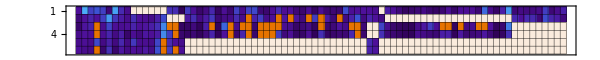
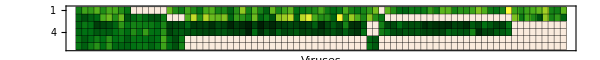
-Graphics- |   
-Graphics- |

```mathematica
Block[{colorLowStandardDeviation=RGBColor[0.9, 0.45, 0.],colorNotInTable=RGBColor[0.9804100067361553, 0.9215680276794109, 0.8666658310700697],virusesSorted,opts={LabelStyle->Directive[FontSize->16],FrameStyle->Directive[Black,Thickness[Small]],TicksStyle->Directive[FontColor->colorTicks,Thickness[Medium]],LegendMarkerSize->100}},
(* Sort the viruses based on how many tables they are in *)
virusesSorted=ReverseSortBy[viruses[All],containingTables];
(* Min/Max values of RMSE and r^2 *)
{arrayCorrelation,arrayRMSE}=ArrayPlot[Switch[#,
"Pearson's r^2",{index,colorTheme,bounds}={3,"DeepSeaColors",{1.0,0}},
"RMSE",{index,colorTheme,bounds}={4,"AvocadoColors",{0,1.2}}
];
Table[
res=If[#=="Pearson's r^2"&&MemberQ[resInterFonville,{virus,table,__,True}],Missing["Low Standard Deviation"],FirstCase[resInterFonville,{virus,table,__}]];
If[MissingQ@res,res,res[[index]]]
,{table,fonvilleTables},{virus,virusesSorted}],ColorFunction->(ColorData[colorTheme][Rescale[#,bounds]]&),PlotLabel->font[#,18],Frame->True,FrameLabel->{None,If[#=="RMSE",font["Viruses",14],None]},FrameTicks->{Range@6,None},ColorFunctionScaling->False,ColorRules->{Missing["Low Standard Deviation"]->colorLowStandardDeviation,Missing["NotFound"]->colorNotInTable},Mesh->True,MeshStyle->Directive[Thickness[0.0005],Black],ImageSize->600,AspectRatio->0.1,PlotRangePadding->None]&/@{"Pearson's r^2","RMSE"};
legArrayCorrelation=BarLegend[{ColorData["DeepSeaColors"][1-#]&,{0,1}},Ticks->Table[j,{j,0,1,0.5}],Evaluate@opts];
legArrayRMSE=BarLegend[{"AvocadoColors",{0,1.2}},Ticks->Table[j,{j,0,1.2,0.4}],Evaluate@opts];
legSwatchCorrelation=SwatchLegend[{colorNotInTable,colorLowStandardDeviation},font[#,14]&/@{"Not in Study","Low Standard Deviation"},LegendFunction->"Frame"];
legSwatchRMSE=SwatchLegend[{colorNotInTable},font[#,14]&/@{"Not in Study"},LegendFunction->"Frame"];
Grid[{{arrayCorrelation,Row[{legArrayCorrelation,"  ",legSwatchCorrelation}]},{arrayRMSE,Row[{legArrayRMSE,"  ",legSwatchRMSE}]}},Spacings->3,Alignment->{Left,Top}]
]
```

### Figure S4: Inter-Table Completion with Multiple Viruses Left Out

Inter-table completion (where a virus is entirely removed from a dataset and imputed via matrix completion) works remarkably well for Fonville Tables S5/S6 and S13/S14 (Studies 3/4 and 5/6). This figure explores how well multiple viruses can be withheld and imputed.

For simplicity, we either use Table S5 to predict values in Table S6 (denoted by Table S5→Table S6 in the figure) or use Table S13 to predict values in Table S14 (denoted by Table S13→Table S14), without looking at the reverse directions.

The rationale behind this choice is that the measurements in Tables S5 and S6 were carried out in 1997 and 1998, respectively, so that measurements in Table S6 could have been informed by the measurements carried out a year earlier for Table S5. Similarly, Tables S13 and S14 were carried out in 2009 and 2010, respectively.

```mathematica
(*Clear[virusesWithheld]
virusesWithheld[table_]:=Block[{},
SeedRandom[12345];
Join@@Table[RandomSample[viruses[table],numWithheld],{numWithheld,1,Length@viruses[table],If[table==="S6",4,2]},{replicates,10}]
]
resWithholdMulti["S6"]=Table[
interTableCompletionFonville[{withheld,"S6"},"TablesToConsider"->{"S5","S6"}],{withheld,virusesWithheld["S6"]}];
resWithholdMulti["S14"]=Table[
interTableCompletionFonville[{withheld,"S14"},"TablesToConsider"->{"S13","S14"}],{withheld,virusesWithheld["S14"]}];*)
```

```mathematica
(*Iconize[resWithholdMulti["S6"],"Leave Multiple Out (Table S6)",Method->Compress]
Iconize[resWithholdMulti["S14"],"Leave Multiple Out (Table S14)",Method->Compress]*)
resWithholdMulti["S6"]=;
resWithholdMulti["S14"]=;
```

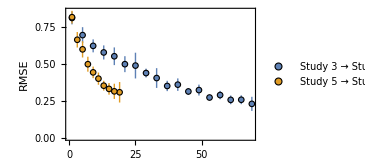

```mathematica
(* Plotting *)
ListPlot[Table[{Length@viruses[table]-Length@#[[1,1]],Around[Mean[#[[All,-2]]],StandardDeviation[#[[All,-2]]]]}&/@SplitBy[resWithholdMulti[table],Length@First@#&],{table,{"S6","S14"}}],]
```

### Figure S5: Fonville Inter-Table Completions using a Subset of Studies

Rather than using the combination of all Fonville tables when performing the inter-table completion, we restrict the completion to only use a subset of tables. In this way, we can determine how well matrix completion works across different types of data (i.e. ferret vs human or vaccination vs infection).

```mathematica
(* === Human->Ferret is equivalent to the inter-table completions to Table S1 === *)
(*resHumanToFerret=Cases[resInterFonville,{_,"S1",__}];*)
(*(* === Ferret->Human uses all the viruses in Table S1 === *)
resFerretToHuman=Table[interTableCompletionFonville[{virus,DeleteCases[containingTables@virus,"S1"]},"TablesToConsider"->Min],{virus,viruses["S1"]}]*)
(*(* === Vaccination->Infection uses Tables S5,S6,S13,S14 to predict Table S3 === *)
resVacToInfect=Table[interTableCompletionFonville[{virus,"S3"},"TablesToConsider"->DeleteCases[containingTables@virus,"S1"]],{virus,Cases[viruses["S3"],virus_/;ContainsAny[containingTables@virus,{"S5","S6","S13","S14"}]]}]*)
(*(* === Infection->Vaccination uses Table S3 to predict Tables S5,S6,S13,S14 === *)
resInfectToVac=Table[interTableCompletionFonville[{virus,Intersection[containingTables@virus,{"S5","S6","S13","S14"}]},"TablesToConsider"->DeleteCases[containingTables@virus,"S1"]],{virus,Cases[viruses["S3"],virus_/;ContainsAny[containingTables@virus,{"S5","S6","S13","S14"}]]}]*)
(*(* === Vaccination->Vaccination (10 years apart) uses Table S5,S6 to predict Tables S13,S14 (or vice versa) === *)
resVacToVac10Years=Join[Table[interTableCompletionFonville[{virus,Intersection[containingTables@virus,{"S5","S6"}]},"TablesToConsider"->{"S5","S6","S13","S14"}],{virus,Cases[viruses["S5"],virus_/;ContainsAny[containingTables@virus,{"S13","S14"}]]}],Table[interTableCompletionFonville[{virus,Intersection[containingTables@virus,{"S13","S14"}]},"TablesToConsider"->{"S5","S6","S13","S14"}],{virus,Cases[viruses["S5"],virus_/;ContainsAny[containingTables@virus,{"S13","S14"}]]}]]*)
(*(* === Vaccination->Vaccination (1 year apart) uses Table S5 to predict Table S6 (or vice versa), or it uses Table S13 to predict Table S14 (or vice versa) === *)
resVacToVac1Year=Join[Table[interTableCompletionFonville[{virus,"S5"},"TablesToConsider"->{"S5","S6"}],{virus,viruses["S5"]}],Table[interTableCompletionFonville[{virus,"S6"},"TablesToConsider"->{"S5","S6"}],{virus,viruses["S5"]}],Table[interTableCompletionFonville[{virus,"S13"},"TablesToConsider"->{"S13","S14"}],{virus,viruses["S13"]}],Table[interTableCompletionFonville[{virus,"S14"},"TablesToConsider"->{"S13","S14"}],{virus,viruses["S13"]}]]*)
```

```mathematica
(*Iconize[resHumanToFerret,"Human→Ferret",Method->Compress]
Iconize[resFerretToHuman,"Ferret→Human",Method->Compress]
Iconize[resVacToInfect,"Vac→Infect",Method->Compress]
Iconize[resInfectToVac,"Infect→Vac",Method->Compress]
Iconize[resVacToVac10Years,"Vac→Vac (10 Years)",Method->Compress]
Iconize[resVacToVac1Year,"Vac→Vac (1 Year)",Method->Compress]*)
{resHumanToFerret,resFerretToHuman,resVacToInfect,resInfectToVac,resVacToVac10Years,resVacToVac1Year}={,,,,,};
```

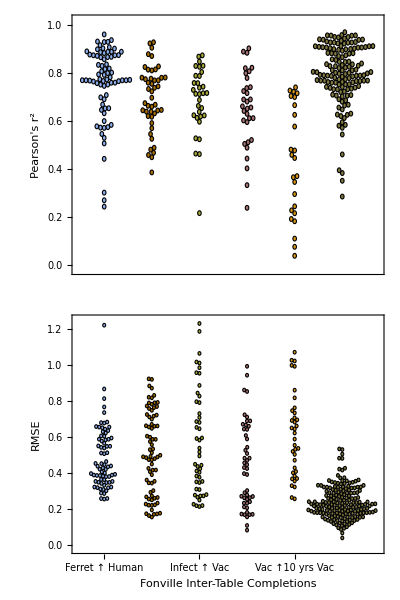

```mathematica
(* Swarm plots *)
{plotRSquared,plotRMSE}=With[{r=0.0105,type=#},
plotRange={{0.45,6.75},{-0.02,If[type==="Pearson's r^2",1.02,1.25]}};
(* Compute r^2 and RMSE for all viruses in each study. For the r^2 analysis, do not consider points where the measured or predicted values have a low standard deviation (<0.2) which artifically inflates the correlation coefficient *)
pnts=Cases[#,{_,_,__,If[type==="Pearson's r^2",(* Remove cases with artifically deflated r^2 *)False,_]}][[All,If[type==="Pearson's r^2",3,4]]]&/@{resHumanToFerret,resFerretToHuman,resVacToInfect,resInfectToVac,resVacToVac10Years,resVacToVac1Year};
swarmPlot[pnts,r,]
]&/@{"Pearson's r^2","RMSE"};
Grid[{{plotRSquared},{plotRMSE}}]
```

### Figure S6: Accuracy of Matrix Completion vs Virus Divergence

Here, we assess how the accuracy of intra-table completion matrix completion depends upon the similarity of the viruses in the dataset.

For each virus V, we choose n other viruses whose amino acid Hamming distance (ΔAA) is greater than some threshold value (x-axis in the figure). n=9 for the influenza data and n=34 for the HIV-1 data. These values are large enough to permit accurate matrix completion but small enough to probe the full range of virus dissimilarity seen in each dataset.

For influenza, the matrix size is fixed at (10 viruses) × (256 sera), with the first virus being the virus of interest

For HIV-1, the matrix size equals (UpTo[35] viruses) × (156 sera), with the first virus being the virus of interest. The number of virus might slightly decrease for a few viruses (down to 30) towards ΔAA=200

For influenza, we only focus on viruses in Fonville Table S6 (chosen because it has nearly-complete data and a large virus panel). For HIV-1, we select a subset of viruses and sera with nearly complete data and a comparable size to Fonville Table S6. The key difference is that the ΔAA between viruses is much larger on average for the HIV-1 strains

```mathematica
(*resFonvilleLargeAA=Association@Table[
minSeqDistToRemove=Prepend[Cases[Union@Table[HammingDistance@@({virusOfInterest,virus}/.replaceSeqFonville),{virus,DeleteCases[viruses["S6"],virusOfInterest]}],val_/;val<30],0];
(* For speed, cut down the number of points on the x-axis *)
minSeqDistToRemove=DeleteCases[minSeqDistToRemove,val_/;(EvenQ[val]&&MemberQ[minSeqDistToRemove,val-1])];
minSeqDistToRemove=DeleteCases[minSeqDistToRemove,val_/;(OddQ[val]&&MemberQ[minSeqDistToRemove,val-1])];
(* Run the matrix completions *)
PrintTemporary[Row[{virusOfInterest,": ",minSeqDistToRemove}]];
virusOfInterest->(analyzeSeqSimilarity[virusOfInterest,#,"S6",10]&/@minSeqDistToRemove)
,{virusOfInterest,viruses["S6"]}]
Iconize[resFonvilleLargeAA,Method->Compress]*)
resFonvilleLargeAA=;
```

```mathematica
leg=LineLegend[Directive[Thick,#]&/@{GrayLevel[0.8],ColorData[97][1]},font[#,14]&/@{"Individual Virus","Average Results"},LegendMarkers->plotMarker[0.04,0.8],LegendFunction->frame,Spacings->{0.2,0.4}];
plotData=DeleteCases[resFonvilleLargeAA,{x_,y_}/;x>30,{2}];
mean={N@Mean[First/@#],If[Length@#==1,First@#,Around[Mean[#],StandardDeviation[#]]]&[Last/@#]}&/@GatherBy[Sort[Join@@Values@plotData],Floor[First[#],2]&];
(*mean=Cases[mean,{x_,y_}/;100<x<200];*)
leg=LineLegend[Directive[Thick,#]&/@{GrayLevel[0.8],ColorData[97][1]},font[#,14]&/@{"Individual Virus","Average Results"},LegendMarkers->plotMarker[0.04,0.8],LegendFunction->frame,Spacings->{0.2,0.4}];
plotFonville=Show[ListPlot[plotData,],ListPlot[MovingAverage[mean,2],PlotMarkers->plotMarker[0.04,0.9],Joined->True,PlotStyle->Thick]];
```

```mathematica
(*table="CatnapMonoclonal";
resCatnap=Association@Table[
minSeqDistToRemove=Prepend[Cases[Union@Table[seqDistance@@({virusOfInterest,virus}/.replaceSeqCatnap),{virus,DeleteCases[virusesOfInterestCatnap,virusOfInterest]}],val_/;val<200],0];
(* For speed, cut down the number of points on the x-axis *)
minSeqDistToRemove=DeleteCases[minSeqDistToRemove,val_/;(ContainsAny[minSeqDistToRemove,Range[Floor[val,5],val-1]])];
(* Run the matrix completions *)
PrintTemporary[Row[{virusOfInterest,": ",minSeqDistToRemove}]];
virusOfInterest->(analyzeSeqSimilarity[virusOfInterest,#,table]&/@minSeqDistToRemove)
,{virusOfInterest,virusesOfInterestCatnap}]
Iconize[resCatnap,Method->Compress]*)
resCatnap=;
```

```mathematica
plotData=DeleteCases[resCatnap,{x_,y_}/;x≤95||x>200,{2}];
mean={N@Mean[First/@#],If[Length@#==1,First@#,Around[Mean[#],StandardDeviation[#]]]&[Last/@#]}&/@GatherBy[Sort[Join@@Values@plotData],Floor[First[#],10]&];
mean=Cases[mean,{x_,y_}/;100<x<200];
plotCatnap=Show[ListPlot[plotData,],ListPlot[mean,PlotMarkers->plotMarker[0.04,0.9],Joined->True,PlotStyle->Thick]];
```

```mathematica
Grid[{{plotFonville,plotCatnap}},Spacings->3]
```

-Graphics-

### Figure S7: Using Prior HIV-1 Measurements to Predict Future Measurements

Using existing Catnap measurements up to a certain year to predict either the most potent or the weakest future measurements. More specifically, what number of potent interactions (IC_50<0.1 μg/mL) or weak interactions (IC_50>10 μg/mL) are identified by N experiments (x-axis).

```mathematica
Grid[Table[predictFutureExperiments[year,searchType],{searchType,{"PotentInteractions","WeakInteractions"}},{year,2017,2019}],Spacings->{2,1},ItemSize->All]
```

-Graphics-

### Figure S8: Inter-Table Completion of Fonville→Vinh

Withholding all 24,000 measurements from one of the six Vinh viruses and predicting them using the Fonville dataset via matrix completion. We note that the absolute magnitude of the predictions are markedly off from the true measurements, although the slope of the best-fit line (colored) is positive, indicating that the rank order of the weakest-to-strongest measurements is accurately predicted.

```mathematica
Grid[Partition[interTableCompletionVinh[#,"Exact"]&/@Range@6,3]]
```

-Graphics-

### Table S1: Datasets Analyzed

Matrix completion statistics for the Fonville tables and the Catnap monoclonal antibody dataset.

```mathematica
resIntraAnalysis=Join[resIntraFonville,resIntraCatnap];
(* Compute statistics *)
vals=(
numMissing=Length@Cases[Table[data[{virus,serum}],{serum,sera[#]},{virus,viruses[#]}],_Missing,All];
fracMissing=100 numMissing/(Length@sera@# Length@viruses@#);
dataTable=Log10@N@Table[dataComplete[{virus,serum}],{serum,sera[#]},{virus,viruses[#]}];
dataTable=dataTable-Mean@Flatten[dataTable];
(* Compute the rank of each Fonville study as the number of singular values required to characterize 95% of the variance *)
rankFonville=(
σVals=SingularValueList[dataTable];
plotData=Transpose[{Range@Length@σVals,Accumulate[σVals^2]/Total[σVals^2]}][[;;UpTo[25]]];
f=Interpolation[plotData];
root=x/.FindRoot[f[x]==0.95,{x,9}]
);

rSquaredLowRankApprox=correlation[DeleteMissing[Log10@N[Join@@Table[{data[{virus,serum}],dataComplete[{virus,serum}]},{serum,sera[#]},{virus,viruses[#]}]],1,All]];
(* Comparing the RMSE of the measured values pre- and post-completion *)
RMSEmeasured=Round[RootMeanSquare[Subtract@@@DeleteMissing[Log10@N[Join@@Table[{data[{virus,serum}],dataComplete[{virus,serum}]},{serum,sera[#]},{virus,viruses[#]}]],1,All]],0.001];
RMSEwithheld=Cases[resIntraAnalysis,{#,__}][[All,{2,4}]][[-1,-1]];
{If[#=!="CatnapMonoclonal","Fonville Table "<>#,"Catnap Monoclonal"],Length@sera@#,Length@viruses@#,Row[{numMissing," (",Round[fracMissing,If[fracMissing<1,0.1,1]],"%)"}],Round@rankFonville,Round[rSquaredLowRankApprox,0.001],Round[RMSEmeasured,0.01],Round[RMSEwithheld,0.01]}
)&/@Append[fonvilleTables,"CatnapMonoclonal"];
Grid[Map[font,Prepend[vals,{"Data","# Antibodies","# Viruses","# Missing","Rank","r^2","RMSE measured","RMSE withheld"}],{2}],]
```

Data | # Antibodies | # Viruses | # Missing | Rank | r^2 | RMSE measured | RMSE withheld
Fonville Table S1 | 35 | 74 | 342 (13%) | 6 | 0.996 | 0.06 | 0.32
Fonville Table S3 | 324 | 57 | 6871 (37%) | 8 | 0.997 | 0.04 | 0.21
Fonville Table S5 | 212 | 70 | 1047 (7%) | 7 | 0.997 | 0.04 | 0.18
Fonville Table S6 | 256 | 70 | 1524 (9%) | 7 | 0.998 | 0.03 | 0.18
Fonville Table S13 | 160 | 20 | 14 (0.4%) | 9 | 0.997 | 0.04 | 0.28
Fonville Table S14 | 160 | 20 | 35 (1%) | 8 | 0.997 | 0.04 | 0.28
Catnap Monoclonal | 373 | 933 | 301853 (87%) | 24 | 1. | 0.03 | 0.77

# Initialization

## Plotting

### Plot Options

```mathematica
(* Color scheme Dark 2 *)
colors={RGBColor[0.45860547189052764, 0.43899629833399423, 0.7019601145242871],RGBColor[0.4001493096820993, 0.40014898705838536, 0.40014881754595555],RGBColor[0.10735368575582693, 0.6201801935350626, 0.4673715774466202],RGBColor[0.39977958986633894, 0.6510770720392438, 0.11722875093558652],RGBColor[0.6509557752826353, 0.4621627671221546, 0.11250229726888727],RGBColor[0.8513180021016765, 0.3717430799229984, 0.008273519282768628]};
{colorMissing,colorWithheld}={RGBColor[0, 0, 1],RGBColor[1., 0.752940145064468, 2.366108526150601*^-6]};
colorTicks=GrayLevel[0.3];
```

```mathematica
Options[plotMarker]={"Type"->"Circle","EdgeColor"->Black,"EdgeThickness"->Tiny};
plotMarker[size:(_Real|_Integer):0.04,opacity:(_Real|_Integer):1,OptionsPattern[]]:={Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],Thickness[OptionValue["EdgeThickness"]],OptionValue["EdgeColor"]}],Switch[OptionValue["Type"],
"Circle",Disk[],
"Square",Rectangle[]
]}],size};
```

```mathematica
(* To format String expressions *)
font[text_,size_:12,opts___]:=Style[text,FontFamily->"Times",size,opts];
```

```mathematica
(* Styling for plot legends *)
frame[leg_,roundingMargin_:0,roundingRadius_:10,frameStyle_:Black]:=Framed[leg,RoundingRadius->roundingRadius,FrameMargins->roundingMargin,FrameStyle->frameStyle,Background->White];
```

### Swarm Plot

```mathematica
(* https://mathematica.stackexchange.com/questions/42585/implementing-a-beeswarm-plot-in-mathematica *)intervalInverse[Interval[]]:=Interval[{-∞,∞}]
intervalInverse[Interval[int__]]:=Interval@@Partition[Replace[Flatten@{int},{
{-∞,mid___,∞}:>{mid},
{-∞,mid__}:>{mid,∞},
{mid__,∞}:>{-∞,mid},
{mid___}:>{-∞,mid,∞}
}],2]
intervalComplement[a_Interval,b__Interval]:=IntervalIntersection[a,intervalInverse@IntervalUnion@b]
```

```mathematica
(* 'data' is assumed to be a sorted vector of numbers *)
(* 'radius' specifies the distance between adjacent ponts *)
(* 'xShift' translates all points to the right *)
(* 'ratio' allows for arbitrary aspect ratios and plot ranges *)
(* 'fracOverlap' tunes how much points should overlap in the x-direction to make the map more compact (value should be between 0 and 1) *)
Clear[swarm]
swarm[data_,radius_,xShift_:0,ratio_:1.,fracOverlap_:0]/;0≤fracOverlap≤1:=Module[{points={},left,right,int},
Do[
int=Interval@@Cases[points,{x_,y_}/;y>(pt- 2radius):>x+(1-fracOverlap)ratio{-1,1} Sqrt[(2radius)^2-(pt-y)^2]];
right=Min@intervalComplement[Interval[{0,Infinity}],int];
left=Max@intervalComplement[Interval[{-Infinity,0}],int];
AppendTo[points,{If[right<-left,right,left],pt}]
,{pt,data}];
{xShift,0}+#&/@points
]
```

```mathematica
ClearAll[swarmPlot]
Options[swarmPlot]=Join[Options@Graphics,{PlotStyle->Automatic,PlotMarkers->Automatic,PlotLegends->None}];
SetOptions[swarmPlot,Frame->True];
SetOptions[swarmPlot,FrameTicks->{None,Automatic}];

(* Handle Missing values *)
swarmPlot[data_,radius:(_?NumericQ|Automatic):Automatic,fracOverlap:(_Real|_Integer):0,opts:OptionsPattern[]]/;MemberQ[data,_Missing,All]:=swarmPlot[DeleteCases[data,{_,_Missing}|_Missing,All],radius,opts]

(* Single dataset without x-coordinates *)
swarmPlot[data_?(VectorQ[#,NumericQ]&),radius:(_?NumericQ|Automatic):Automatic,fracOverlap:(_Real|_Integer):0,opts:OptionsPattern[]]:=swarmPlot[{{1,#}&/@data},radius,opts]
(* Single dataset with x-coordinates *)
swarmPlot[data_?(MatrixQ[#,NumericQ]&)/;Equal@@First/@data,radius:(_?NumericQ|Automatic):Automatic,fracOverlap:(_Real|_Integer):0,opts:OptionsPattern[]]:=swarmPlot[{data},radius,opts]
(* Multiple datasets without x-coordinates *)
swarmPlot[data:{__?(VectorQ[#,NumericQ]&)},radius:(_?NumericQ|Automatic):Automatic,fracOverlap:(_Real|_Integer):0,opts:OptionsPattern[]]:=swarmPlot[MapIndexed[Thread@{First@#2,#}&,data],radius,opts]

(* Multiple datasets with x-coordinates *)
swarmPlot[data:{__?(MatrixQ[#,NumericQ]&)},pointRadius:(_?NumericQ|Automatic):Automatic,fracOverlap:(_Real|_Integer):0,opts:OptionsPattern[]]:=
Module[{plotStyle=OptionValue[PlotStyle],plotLegends=OptionValue[PlotLegends],aspectRatio=OptionValue[AspectRatio],plotRange=OptionValue[PlotRange],plotRangeRatio,colors,radius=pointRadius,plot},
(* Quality checks *)
If[!And@@(Equal@@First/@#&/@data),Echo["Dataset indices not uniform","Error!"];Break[]];

(* Radius selection *)
If[radius===Automatic,radius=2 Mean[Join@@Differences/@Sort/@data[[All,All,-1]]]];

(* PlotRange *)
If[plotRange===Automatic,plotRange={{First@#-1,Last@#+1}&[MinMax@data[[All,1,1]]],MinMax@data[[All,All,2]]}
];
plotRangeRatio=Divide@@Subtract@@@plotRange;
If[aspectRatio===Automatic,aspectRatio=1/plotRangeRatio];

(* PlotStyle *)
colors=
Switch[plotStyle,
Automatic,ColorData[97]/@Range@Length@data,
_List,plotStyle,
_,plotStyle/@Range@Length@data
];

(* Plotting *)
plot=Graphics[{EdgeForm[{Thickness[Tiny],Black}],MapIndexed[{colors[[First@#2]],Disk[#1,0.95 radius{plotRangeRatio aspectRatio,1}]&/@swarm[Sort[Last/@#],radius,#[[1,1]],plotRangeRatio aspectRatio,fracOverlap]}&,data]},opts,Frame->OptionValue[Frame],FrameTicks->OptionValue[FrameTicks]];
Switch[plotLegends,
(* No legend *)
None,plot,
(* Labels of legend provided *)
_List,Grid[{{plot,PointLegend[colors,plotLegends]}},Spacings->2],
(* Complete legend provided *)
_,Grid[{{plot,plotLegends}},Spacings->2]
]
]
```

```mathematica
(*(* Example of how you can manipulate the plot range and aspect ratio. The size of the circles will adjust to accomodate *)
pnts=;
{swarmPlot[pnts,0.012,PlotRange->{{0.5,2.5},{0,1.3}},ImageSize->250],swarmPlot[pnts,0.012,PlotRange->{{0.5,2.5},{0,1.3}},ImageSize->250,AspectRatio->1]}
(* Example of how you can tune the amount of overlap in the x-direction to make the plot more compact *)
swarmPlot[pnts,0.012,#,PlotRange->{{0.5,2.5},{0,1.3}},ImageSize->200,AspectRatio->1]&/@{0,0.3,0.6}*)
```

```mathematica
(*(* Example data *)
SeedRandom[12345]
data1=RandomVariate[ExponentialDistribution[1],200];
data2=RandomVariate[NormalDistribution[2,1],200];
(* Plot 1 or 2 daasets *)
plot1=swarmPlot[data1];
plot2=swarmPlot[MapIndexed[Thread@{2First@#2,#}&,{data1,data2}]];
(* Change the color while keeping the radius selection automatic *)
plot3=swarmPlot[{data1,data2},Automatic,PlotStyle->ColorData[95]];
(* Specify the circle radius explicitly in plot coordinates *)
plot4=swarmPlot[data2,0.2,ImageSize->200];
Grid[{{plot1,plot2,plot3,plot4}},Spacings->3]*)
```

## Importing Data

#### Helper Functions

```mathematica
(* Number of Fonville tables containing a virus *)
containingTables[virus_]:=Cases[fonvilleTables,table_/;MemberQ[viruses[table],virus]]
(*(* Example Usage *)
containingTables/@viruses[All]*)
```

```mathematica
(* Fraction of variance explained via Pearson's correlation coefficient squared *)
Clear[correlation]
correlation[data_/;MatchQ[Min[StandardDeviation/@Transpose@data],0|0.]]:=Missing[]
correlation[data_]:=(Correlation@@Transpose@data)^2
```

```mathematica
(* Coefficient of determination R^2 *)
rSquared[data_]:=Module[{mean=Mean[data[[All,2]]]},
1-Total[(#[[1]]-#[[2]])^2&/@data]/Total[(#[[2]]-mean)^2&/@data]
]
```

```mathematica
(* Determine the year of isolation of a virus *)
(* When multiple strains have the same sequence (and hence their names are concatenated with a ";"), take the max year of circulation over all viruses *)
Clear[virusYear]
virusYear[str_String/;!StringContainsQ[str,";"]]:=Module[{year=StringDelete[Last@StringSplit[str,"/"],"_MDCK"|"_EGG"|"-egg"]},
Which[
StringMatchQ[year,DigitCharacter~~DigitCharacter~~DigitCharacter~~DigitCharacter],ToExpression@year,

StringMatchQ[year,DigitCharacter~~DigitCharacter]&&ToExpression@year<50,
ToExpression@year+2000,

StringMatchQ[year,DigitCharacter~~DigitCharacter]&&50≤ToExpression@year<100,
ToExpression@year+1900,

True,
$Failed
]
]
```

```mathematica
(* Fit based on minimizing the perpendicular distance to the best-fit line *)
fitPerp[fitData_,showLineQ_:True]:=Block[{n=Length@fitData,xAvg=Mean@N@fitData[[All,1]],yAvg=Mean@N@fitData[[All,2]],B,b,a,numerator,denominator},
numerator=(Total[fitData[[All,2]]^2]-n yAvg^2)-(Total[fitData[[All,1]]^2]-n xAvg^2);
denominator=n xAvg yAvg-Total[Times@@@fitData];
If[denominator==0.,Return[$Failed]];
B=1./2 numerator/denominator;
b=-B+Sqrt[B^2+1];
a=yAvg-b xAvg;
If[showLineQ,
(* Return best-fit line *)
a+b x,
(* Return RMSE around best-fit line *)
Sqrt@Mean[(fitData[[All,2]]-(a+b fitData[[All,1]]))^2/(1+b^2)]
]
]
```

```mathematica
(* === Sequence comparison among Catnap viruses === *)
(* Amino acid similarity - blank letters are considered a mismatch *)
Clear[seqDistance]
seqDistance[seq1_,seq2_]:=HammingDistance@@{seq1,seq2}-Length@Cases[Transpose@Characters@{seq1,seq2},{"-",Except["-"]}|{Except["-"],"-"}]
```

```mathematica
(* Find a subset of viruses with (at least) a specified amount of sequence dissimilarity *)
Clear[analyzeSeqSimilarity]
analyzeSeqSimilarity[virusOfInterest_,minSeqDistToRemove_,table_:"S6",numViruses_:35,multipleRunsQ_:False]:=Block[{vals,virusesOfInterest,seraOfInterest,virusSubset,posMeasured,posWithheld,dataMeasurements,dataPreCompletion},
virusesOfInterest=If[MemberQ[fonvilleTables,table],viruses[table],virusesOfInterestCatnap];
seraOfInterest=If[MemberQ[fonvilleTables,table],sera[table],seraOfInterestCatnap];
(* Virus of interest and the 'numViruses'-1 viruses with the closest viruses with ΔAA>'minSeqDistToRemove' *)
virusSubset=Prepend[First/@DeleteCases[SortBy[{#,seqDistance@@({virusOfInterest,#}/.If[MemberQ[fonvilleTables,table],replaceSeqFonville,replaceSeqCatnap])}&/@virusesOfInterest,Last],{virus_,dist_}/;dist≤minSeqDistToRemove][[;;UpTo[numViruses-1]]],virusOfInterest];
dataMeasurements=N@Table[data[{virus,serum}],{virus,virusSubset},{serum,seraOfInterest}]/.val_Real:>Log10@val;
posMeasured=Cases[Position[dataMeasurements,Except[_Missing],{2},Heads->False],{1,_}];
SeedRandom[12345];
{Min[seqDistance@@({virusOfInterest,#}/.If[MemberQ[fonvilleTables,table],replaceSeqFonville,replaceSeqCatnap])&/@Rest@virusSubset],
vals=Table[
posWithheld=RandomSample[posMeasured,Round[0.2 Length@posMeasured]];
dataPreCompletion=ReplacePart[dataMeasurements,posWithheld->Missing["Withheld"]];
RootMeanSquare[Subtract@@@Transpose@{Extract[RPCA[dataPreCompletion],posWithheld],Extract[dataMeasurements,posWithheld]}]
,{numRuns,If[multipleRunsQ,3,1]}];
If[multipleRunsQ,MeanAround@vals,First@vals]}
]
```

### Influenza: Fonville 2014

Importing the  raw measurements from Fonville 2014 into the variable data:

Table S1: This is the transpose of the original Fonville Table S1, so that the first column represents sera and the first row represents viruses. All other tables were already ordered in this format, so their un-transposed versions are imported.

Some viruses with the same name are labeled with underscores in Table S1 but forward slashes in the other tables, and we unify their names upon import ("HN196_2009"→"HN196/2009"). We also unified names that used short virus names in some tables but long virus names in other tables ("JO/33/94"→"A/JOHANNESBURG/33/94").

Tables S5-S6, S13-S14: The pre-vaccination and post-vaccination sera are distinguished by either having "_Pre" or "_Post" at the end of the serum name

All sera have their Table designation (either S1, S3, S5, S6, S13, or S14) in their name as "_TableX"

```mathematica
(* List of all Fonville supplementary tables *)
fonvilleTables={"S1","S3","S5","S6","S13","S14"};
```

```mathematica
Block[{rawData,table},
MapIndexed[(
rawData=#;
table=fonvilleTables[[First@#2]];
sera[table]=rawData[[2;;,1]];
viruses[table]=rawData[[1,2;;]];
(* Import values in the form: data[{virus,antibody}] *)
Do[
data[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
)&
,]
];
```

Each table was individually matrix completed (intra-table completion), and the resulting completions are stored in dataComplete.

```mathematica
(*(* Example: Intra-table completing Table S1 *)
RPCA[Table[N@data[{virus,serum}],{serum,sera["S1"]},{virus,viruses["S1"]}],"LogData"->True]*)
```

```mathematica
Block[{rawData},
MapIndexed[(
rawData=#;
(* Import values in the form: dataComplete[{virus,antibody}] *)
Do[
dataComplete[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
)&
,]
];
```

Creating a cumulative list of viruses and sera in Fonville, and then creating the combined dataset containing all six tables. The resulting matrix is (inter-table) matrix completed in the variable dataAllComplete where every virus-serum pair is imputed.

```mathematica
(* Combined viruses and sera in all Fonville tables *)
sera[All]=Join@@sera/@fonvilleTables;
viruses[All]=Sort@DeleteDuplicates[Join@@viruses/@fonvilleTables];
(* Slight aesthetic reordering *)
viruses[All]=ReplacePart[viruses[All],
{21->viruses[All][[22]],
22->viruses[All][[21]],
41->viruses[All][[42]],
42->viruses[All][[41]]
}
];
```

```mathematica
(*(* Example: Inter-table completing all Fonville tables *)
RPCA[Table[N@data[{virus,serum}],{serum,sera[All]},{virus,viruses[All]}],200,"LogData"->True]*)
```

```mathematica
Block[{rawData=},
(* Import values in the form: dataAllComplete[{virus,antibody}] *)
Do[
dataAllComplete[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
];
```

```mathematica
(* HA Sequences *)
replaceSeqFonville=;
```

### Influenza: Vinh 2021

Importing data from Vinh 2021: Age-seroprevalence curves for the multi-strain structure of influenza A virus

We only consider the six H3N2 viruses, since all viruses in Fonville 2014 are H3N2

The following 4/6 viruses exactly match to the Fonville strains:

Vinh H3-2003 (H3N2 A/Wyoming/3/2003) → Fonville H3N2 A/Wyoming/3/2003

Vinh H3-2005 (H3N2 A/Wisconsin/67/2005) → Fonville H3N2 A/Wisconsin/67/2005

Vinh H3-2007 (H3N2 A/Brisbane/10/2007) → Fonville H3N2 A/Brisbane/10/2007

Vinh H3-2011 (H3N2 A/Victoria/361/2011) → Fonville H3N2 A/Victoria/361/2011

The other 2/6 viruses have close homologues in the Fonville panel, so we match them up accordingly:

Vinh H3-1968 (H3N2 A/Aichi/2/1968) → Fonville A/Bilthoven/16190/1968 [differs by 3 amino acids in HA]

Vinh H3-2009 (H3N2 A/Victoria/210/2009) → Fonville A/Hanoi/EL201/2009 [differs by 7 amino acids in HA]

```mathematica
Block[{rawData=},
sera["Vinh"]=rawData[[2;;,1]];
viruses["Vinh"]=rawData[[1,2;;]];
(* Import values in the form: data[{virus,antibody}] *)
Do[
data[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
];
```

```mathematica
virusesOfInterestVinh=Join[Reverse@viruses["Vinh"],DeleteCases[ReverseSortBy[Cases[viruses[All],virus_/;2005≤virusYear@virus≤2011],virusYear@#&],Alternatives@@viruses["Vinh"]]]
```

{A/VICTORIA/361/2011,HN201/2009,A/BRISBANE/10/2007,A/WISCONSIN/67/2005,A/WYOMING/3/2003,BI/16190/68,VN053/2010,VN021/EL444/2010,VN020/EL443/2010,VN019/EL442/2010,A/VICTORIA/8/2010,VN018/EL204/2009,HN206/2009,HN196/2009,A/VICTORIA/500/2009,A/VICTORIA/208/2009,A/PERTH/16/2009,VN017/EL140/2008,VN016/EL135/2008,VN015/EL134/2008,A/URUGUAY/716/2007,A/PERTH/27/2007,A/BRISBANE/3/2005}

### HIV-1: Catnap

#### Downloading the latest data

You can easily download the latest Catnap data from the Downloads page. Select Assay, import it as a TSV file, and use either the IC50 (for monoclonal antibodies) or ID50 (for polyclonal sera).

Sera starting with "Polyclonal" represent polyclonal sera

Antibody mixtures containing 2+ antibodies will have a "+" in their name. In addition, there are some multi-specific antibodies with forwards slashes “/” in their name. For simplicity, we remove all antibody mixtures and multi-specific antibodies from our monoclonal antibody dataset

We downloaded the Catnap dataset in March 2021

#### Catnap Database

```mathematica
(* List both Catnap tables *)
catnapTables={"CatnapMonoclonal","CatnapPolyclonal"};
```

```mathematica
Block[{rawData,table},
MapIndexed[(
rawData=#;
table=catnapTables[[First@#2]];
sera[table]=rawData[[2;;,1]];
viruses[table]=rawData[[1,2;;]];
(* Import values in the form: data[{virus,antibody}] *)
Do[
data[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
)&
,]
];
```

There is a key difference when matrix completing the Catnap monoclonal and polyclonal datasets:

For polyclonal sera, larger ID_50 titers represent a stronger antibody response (as in the Fonville dataset). However, for the monoclonal antibody dataset, smaller IC_50 represent a stronger antibody response

To account for this, we use the "InvertData"→True option when matrix completing the monoclonal antibody dataset. This inverts the IC_50 values (sending value→1/value) before matrix completion and then undoes this operation after completion

```mathematica
(*(* Example: Intra-table completing the Catnap polyclonal serum data *)
RPCA[Table[N@data[{virus,serum}],{serum,sera["CatnapPolyclonal"]},{virus,viruses["CatnapPolyclonal"]}],200,"LogData"->True]
(* Example: Intra-table completing the Catnap monoclonal serum data *)
RPCA[Table[N@data[{virus,serum}],{serum,sera["CatnapMonoclonal"]},{virus,viruses["CatnapMonoclonal"]}],200,"LogData"->True,"InvertData"->True]*)
```

```mathematica
Block[{rawData,table},
MapIndexed[(
rawData=#;
table=catnapTables[[First@#2]];
sera[table]=rawData[[2;;,1]];
viruses[table]=rawData[[1,2;;]];
(* Import values in the form: data[{virus,antibody}] *)
Do[
dataComplete[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
)&
,]
];
```

#### HA Sequences

In Figure S6, we restrict our attention to a more complete subset of the Catnap data (only considering viruses measured against ≥150 sera, sera measured against ≥50 viruses). The rationale is that because these viruses may be measured against completely different sera, you will not see an effect of removing a virus with a small ΔAA unless both viruses were measured against the same serum samples. This effect is diminished when the dataset is more complete.

```mathematica
replaceSeqCatnap=;
```

```mathematica
(* Catnap viruses with sequences and ≥150 measurements *)
virusesOfInterestCatnap=Cases[First/@DeleteMissing[replaceSeqCatnap,1,All],virus_/;Length@DeleteMissing@Table[data[{virus,serum}],{serum,sera["CatnapMonoclonal"]}]≥150];
seraOfInterestCatnap=Cases[sera["CatnapMonoclonal"],serum_/;Length@DeleteMissing@Table[data[{virus,serum}],{virus,virusesOfInterestCatnap}]≥50];
```

#### Year Measurements were Taken

```mathematica
yearCatnapMeasurementAbVirus=;
yearCatnapMeasurementAb=;
yearCatnapMeasurementVirus=;
```

## Matrix Completion

### Methods of Completion

#### Robust PCA

Algorithm information from Candes 2009 [open this cell for details]

This algorithm solves the following problem for a matrix M:

Minimize | (||L||)_*+λ (||S||)_1
Subject to | L+S=M

The key changes I implemented were: (1) forcing the low-rank approximating matrix L to exactly equal the measured values and (2) setting λ=0

With these changes, Y=0 at each step and S=P_missing[-L] is equal to -L at the missing values and 0 elsewhere. Essentially, it seems like I am minimizing the nuclear norm with exact fidelity to the data, so it is not too surprising that this method is similar to nuclear norm minimization

I am not sure if this change is optimal or robust, although it seems to work for intra-table completion for the Fonville data. Ultimately, I would like to read the paper to understand the algorithm and see whether my change makes sense, or if there is a better way to implement it

With this change, the optimal value of λ appears to be 0

Larger values of μ tend to yield better results (up to a point), but require more iterations to converge. Default is μ=0.7

I implemented a termination condition based on how similar successive L matrices are to one another. This is pretty ad hoc, but it seemed to work for Fonville intra-table completion. Sometimes the termination condition is not reached, in which case I should ensure that I have added enough iterations for the algorithm to fully converge on the missing values

From my trials on Fonville intra-table completion, Min subtraction does the best, although Mean or No Subtraction do pretty similarly

The Full rank method appears to do the best, although there is the possibility that for very large matrices, using a smaller rank may yield the same solution but faster

The RandomizedSingularValueDecomposition algorithm always took ~2x longer than the standard SVD algorithm, so I have removed that feature entirely

```mathematica
Clear[RPCAShrink,RPCAThreshold];
(* Shrink a value towards zero (by τ) *)
RPCAShrink[matrix_,0]:=matrix;
RPCAShrink[matrix_,τ_]:=Sign[matrix]*Ramp[Abs[matrix]-τ];
(* Soft-thresholding: SVD with singular values shrunk towards zero *)
RPCAThreshold[matrix_,τ_,rank_]:=Block[{U,Σ,V},
{U,Σ,V}=SingularValueDecomposition[matrix,rank];
U.RPCAShrink[Σ,τ].Transpose[V]
];
```

Options:

"ShiftType": Preprocessing the input matrix through different normalization schemes

None: Does not perform any normalization

Min: Subtract the minimum value from all observed entries

Mean: Subtract the mean value from all observed entries

"LogData": If True, take Log_10 of all values in the input matrix before performing matrix completion (if False, leaves the values untouched). In either case, the values in the completed matrix are not logged (i.e. they are exponentiated by 10 after matrix completion if this option value is True)

"InvertData": If True, take 1/value for each entry in the input matrix before performing matrix completion (if False, leaves the values untouched). In either case, the values in the completed matrix are not inverted (i.e. they are inverted again after matrix completion if this option value is True)

"Rank": The rank of the SVD to use in each iteration. By default, we use the full rank of the input matrix

"ShowIntermediateIterations": With the option value None, return the final approximation. With an Integer value, Llist contains the partial results of the completed matrix whenever the iteration is a multiple of this option value

```mathematica
(* https://github.com/dganguli/robust-pca *)
(* See Algorithm 1 in: https://arxiv.org/pdf/0912.3599.pdf *)
(* Parameter λ has been fixed to 0, simplifying the algorithm *)
ClearAll[RPCA];
RPCA::usage="RPCA[matrix, iterations, tolerance, μ] performs Robust PCA decomposition of matrix, returning the low rank matrix L";
Options[RPCA]={"ShiftType"->Min,"LogData"->False,"InvertData"->False,"Rank"->Full,"ShowIntermediateIterations"->None};
(* matrixRaw: Partially observed matrix to be completed *)
(* numIterations: Algorithm terminates after (at most) this number of iterations *)
(* tolerance: Algorithm terminates if RMSE of withheld values changes by less than this value *)
(* μ: Hyperparameter to determine the size of soft-thresholding at each iteration *)
RPCA[matrixRaw_?MatrixQ,numIterations_Integer:2000,tolerance_Real:10^-6.,μ_Real:0.7,options:OptionsPattern[]]:=Catch[
Block[{rank=OptionValue["Rank"],μInv=1.0/μ,count=0,error=∞,shift,L,Lnew,posMissing,posMeasured,originalMeasured,matrix,blank,reapLists},
matrix=N@matrixRaw/._data|_dataComplete->Missing[];
posMissing=Position[matrix,_Missing,{2},Heads->False];
posMeasured=Position[matrix,Except[_Missing],{2},Heads->False];
(* Whether to transform values into Log10 before completing *)
matrix=matrix/.Which[
TrueQ@OptionValue["LogData"],{val_Real:>If[TrueQ@OptionValue["InvertData"],-1,1]Log10@val},
TrueQ@OptionValue["InvertData"],{val_Real:>1/val},
True,{}
];
(* Whether to use the full matrix rank or decreased rank *)
rank=Which[
rank===Full,Min@Dimensions@matrix,
MatchQ[rank,rank_Integer/;0<rank≤Min@Dimensions@matrix],rank,
True,Throw[$Failed]
];
(* Whether to center the matrix by min-/mean-subtracting *)
shift=Switch[OptionValue["ShiftType"],
Min|Mean,OptionValue["ShiftType"]@DeleteMissing@Flatten@matrix,
None,0.
];
matrix=ReplacePart[matrix-shift,posMissing->0.];
(* Constrain matrix to exactly match the measured values *)
originalMeasured=Thread[posMeasured->Extract[matrix,posMeasured]];
(* Robust PCA Algorithm *)
L=matrix;
Llist=Last@Reap[
While[count<numIterations&&error>tolerance,
Lnew=RPCAThreshold[L,μInv,rank];
error=RootMeanSquare@Extract[L-Lnew,posMissing];
(* Measured values are unchanged *)
L=ReplacePart[Lnew,originalMeasured];
If[MatchQ[OptionValue["ShowIntermediateIterations"],_Integer]&&Divisible[count,OptionValue["ShowIntermediateIterations"]],Sow[{count+1,L+shift},"L"]];
count++
],"L"];
Llist=Join@@Llist;
(* Return the low-rank approximation of the matrix *)
Which[
TrueQ@OptionValue["LogData"],
Llist[[All,-1]]=10^(If[TrueQ@OptionValue["InvertData"],-1,1]Llist[[All,-1]]);
10^(If[TrueQ@OptionValue["InvertData"],-1,1](L+shift)),

TrueQ@OptionValue["InvertData"],
Llist[[All,-1]]=1/Llist[[All,-1]];
1/(L+shift),

True,L+shift
]
]
];
```

```mathematica
(*(* === Example usage === *)
(* Prepare Fonville Table S1 with 70% observed fraction. Values are given as Subscript[log, 10][titer] *)
{Xcomplete,Xincomplete}=prepareIntraTableCompletion["S1",0.7];
posWithheld=Position[Xincomplete,Missing["Withheld"]];
(* Perform robust PCA and compute the RMSE error of the withheld values *)
res=RPCA[Xincomplete,"ShowIntermediateIterations"->10];
Echo[RootMeanSquare[Subtract@@@Transpose@{Extract[res,posWithheld],Extract[Xcomplete,posWithheld]}],"RMSE for withheld values:"];
(* Plot the prediction error as a function of the # of iterations [blue] as well as the RMSE between successive iterations [gold] *)
ListPlot[{Transpose@{First/@Llist,RootMeanSquare[Subtract@@@Transpose@{Extract[#,posWithheld],Extract[Xcomplete,posWithheld]}]&/@Last/@Llist},Transpose@{Rest[First/@Llist],RootMeanSquare@Extract[#[[1]]-#[[2]],posWithheld]&/@Partition[Last/@Llist,2,1]}},]*)
```

#### Nuclear Norm Minimization

Semidefinite programming approach to minimizing the nuclear norm. Since the nuclear norm is the convex relaxation of matrix rank, this presents a more computationally efficient way of minimizing matrix rank.

Options:

"ShiftType": Preprocessing the input matrix through different normalization schemes

None: Does not perform any normalization

Min: Subtract the minimum value from all observed entries

Mean: Subtract the mean value from all observed entries

"LogData": If True, take Log_10 of all values in the input matrix before performing matrix completion (if False, leaves the values untouched). In either case, the values in the completed matrix are not logged (i.e. they are exponentiated by 10 after matrix completion if this option value is True)

"InvertData": If True, take 1/value for each entry in the input matrix before performing matrix completion (if False, leaves the values untouched). In either case, the values in the completed matrix are not inverted (i.e. they are inverted again after matrix completion if this option value is True)

```mathematica
Clear[symmetricMatrix]
symmetricMatrix[var_,size_]:=Normal@SymmetrizedArray[{j_,k_}:>Indexed[var,{j,k}],{size,size},Symmetric[{1,2}]]
```

```mathematica
ClearAll[nuclearNormMinimization]
Options[nuclearNormMinimization]={"ShiftType"->Min,"LogData"->False,"InvertData"->False};
nuclearNormMinimization[matrixRaw_?MatrixQ,options:OptionsPattern[]]:=Block[{shift,matrix,x,posMissing,n,m,U,V,mat,u,v},
(* Whether to transform values into Log10 before completing *)
matrix=N@matrixRaw/.Which[
TrueQ@OptionValue["LogData"],{val_Real:>If[TrueQ@OptionValue["InvertData"],-1,1]Log10@val},
TrueQ@OptionValue["InvertData"],{val_Real:>1/val},
True,{}
];
(* Whether to center the matrix by min-/mean-subtracting *)
shift=Switch[OptionValue["ShiftType"],
Min|Mean,OptionValue["ShiftType"]@DeleteMissing@Flatten@matrix,
None,0.
];
matrix=matrix-shift;
(* Change all Missing elements to Indexed elements that can be solved numerically *)
matrix=ReplacePart[matrix,#->Indexed[x,#]&/@Position[matrixRaw,_Missing]];
(* Set up SemidefiniteOptimization *)
{n,m}=Dimensions@matrix;
U=symmetricMatrix[u,n];
V=symmetricMatrix[v,m];
mat=Transpose@Join[Transpose@Join[U,Transpose[matrix]],Transpose@Join[matrix,V]];
(* Complete the missing entries *)
Which[
TrueQ@OptionValue["LogData"],10^(If[TrueQ@OptionValue["InvertData"],-1,1](matrix+shift)),
TrueQ@OptionValue["InvertData"],1/(matrix+shift),
True,matrix+shift
]/.SemidefiniteOptimization[Tr[U]+Tr[V],mat(\[VectorGreaterEqual])_("SemidefiniteCone")0,Variables@{matrix,U,V},Method->"SCS"]
]
```

```mathematica
(* Nuclear norm of a matrix *)
nuclearNorm[mat_]:=Total@SingularValueList@mat
(* Nuclear norm (alternate, slower formulation) *)
(*nuclearNorm[mat_]:=Tr[MatrixPower[ConjugateTranspose[mat].mat,1./2]]*)
```

Example completion

```mathematica
(*pos={{1,2},{3,4},{5,1},{2,4}};
X=# Range@5&/@ Range@5;
(X[[Sequence@@#]]=Missing[])&/@pos;
(X//MatrixForm)->(nuclearNormMinimization[X]//MatrixForm)//Timing*)
```

Testing out how completion scales with the size of the matrix

```mathematica
(*lowRankMatrix[rank_,{n_,m_},fracMissing_:0.1]:=(
SeedRandom[12345];
Xcomplete=X=Sum[RandomReal[{-1,1},n]⊗RandomReal[{-1,1},m],{i,rank}];
numMissing=Round[fracMissing Times@@Dimensions@X];
pos=Transpose@{RandomInteger[{1,First@Dimensions@X},numMissing],RandomInteger[{1,Last@Dimensions@X},numMissing]};
(X[[Sequence@@#]]=Indexed[x,#])&/@pos;
X
);*)
```

### Completion Analysis

#### Intra-Table Completion

```mathematica
(* Generate Fonville and Catnap intra-table completion runs *)
ClearAll[intraTableComplete]
Options[intraTableComplete]={"SeedRandom"->12345,"MaxIterations"->1000,"NumRuns"->10,"ShiftType"->Min,"LogData"->True,"InvertData"->False};
intraTableComplete[table_,observedFrac_,OptionsPattern[]]:=Block[{dataMeasured,nTot,pos,dataPreCompletion,nRemove,posWithheld,rowsFullyMissing,colsFullyMissing,dataPreCompletionClean,dataMeasuredClean,posWithheldClean,resMatrixCompletion},
SeedRandom[OptionValue["SeedRandom"]];
dataMeasured=Table[data[{virus,serum}],{serum,sera[table]},{virus,viruses[table]}]/.{Missing[]|_data->Missing["Not Measured"]};
(* Total number of measurements in the table (counting missing and non-missing) *)
nTot=Times@@Dimensions@dataMeasured;
(* Position of non-missing elements *)
pos=Position[dataMeasured,Except[_Missing],{2},Heads->False];
(* Remove 'nRemove' entries to get an observedFraction==(Length@pos-nRemove)/nTot *)
If[observedFrac>Length@pos/nTot,
Echo["Max observed fraction in Table "<>table<>" is "<>ToString@Round[Length@pos/nTot,0.01],"Warning!"];
Return[Missing["NotComputed"]]
];
nRemove=Round[Length@pos-nTot observedFrac];
(* Return {table, observed fraction, average Pearson's r^2, average RMSE} *)
Join[{table,observedFrac},Around[Mean@#,StandardDeviation@#]&/@Transpose@Table[
dataPreCompletion=dataMeasured;
posWithheld=RandomSample[pos,nRemove];
dataPreCompletion=ReplacePart[dataPreCompletion,posWithheld->Missing["Withheld"]];
(* Remove any row/column with all Missing values. These cannot be inferred (and will mess up Pearson's Correlation) *)
rowsFullyMissing=Position[dataPreCompletion,{_Missing..}];
colsFullyMissing=Position[Transpose@dataPreCompletion,{_Missing..}];
{dataPreCompletionClean,dataMeasuredClean}=Transpose@Delete[Transpose@Delete[#,rowsFullyMissing],colsFullyMissing]&/@{dataPreCompletion,dataMeasured};
(* The withheld values may have been moved if some of the rows/columns were fully Missing *)
posWithheldClean=Position[dataPreCompletionClean,Missing["Withheld"],{2},Heads->False];
(* Matrix complete *)
resMatrixCompletion=Transpose[Log10@N@Extract[#,posWithheldClean]&/@{RPCA[dataPreCompletionClean,OptionValue["MaxIterations"],"ShiftType"->OptionValue["ShiftType"],"LogData"->OptionValue["LogData"],"InvertData"->OptionValue["InvertData"]],dataMeasuredClean}];
{correlation@resMatrixCompletion,RootMeanSquare[Subtract@@@resMatrixCompletion]}
,{run,OptionValue["NumRuns"]}]]
]
```

```mathematica
(*(* Intra-table completions for each Fonville table *)
resIntraFonville=DeleteMissing[Join@@Table[intraTableComplete[table,fracObserved],{table,fonvilleTables},{fracObserved,{0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9}}]]
Iconize[resIntraFonville,"Fonville Intra-Table Completion Results"]*)
(* === Canned results === *)
resIntraFonville=;
```

```mathematica
(*(* Intra-table completions for the monoclonal antibody data *)
resIntraCatnap=Table[intraTableComplete["CatnapMonoclonal",fracObserved,"InvertData"->True],{fracObserved,{0.04,0.07,0.1,0.132}}];
Iconize[resIntraCatnap,"Catnap Intra-Table Completion Results"]*)
(* === Canned results === *)
resIntraCatnap=;
```

#### Inter-Table Completion

Combining the six Fonville 2014 datasets and performing inter-table completion between them

```mathematica
ClearAll[interTableCompletionFonville]
Options[interTableCompletionFonville]={"TablesToConsider"->All,"MaxIterations"->200,"ShiftType"->Min,"LogData"->True,"InvertData"->False};
interTableCompletionFonville[{virusOfInterest_,tableOfInterest_},OptionsPattern[]]:=Block[{multipleVirusQ,tables,listSera,listViruses,posWithheld,dataMeasurements,dataPreCompletion,resMatrixCompletion},
(* True if multiple viruses are withheld *)
multipleVirusQ=If[MatchQ[virusOfInterest,_String],False,True];
(* Which Fonville tables to consider *)
tables=Switch[OptionValue["TablesToConsider"],
(* Using data from all Fonville tables *)
All,fonvilleTables,
(* Only using the tables containing measurements for the withheld virus *)
Min,If[multipleVirusQ,Union[Join@@containingTables/@virusOfInterest],containingTables[virusOfInterest]],
(* Tables to use specified in the option *)
_,OptionValue["TablesToConsider"]
];
listSera=Join@@sera/@tables;
listViruses=DeleteDuplicates[Join@@viruses/@tables];
posWithheld=Tuples[Join@@@{Position[listSera,Alternatives@@If[MatchQ[tableOfInterest,_String],sera[tableOfInterest],Join@@sera/@tableOfInterest]],Position[listViruses,If[multipleVirusQ,Alternatives@@virusOfInterest,virusOfInterest]]}];

dataMeasurements=N@Table[data[{virus,serum}],{serum,listSera},{virus,listViruses}]/.{_data|_Missing->Missing["Not Measured"]};
dataPreCompletion=ReplacePart[dataMeasurements,posWithheld->Missing["Withheld"]];
(* Matrix complete *)
resMatrixCompletion=DeleteMissing[Transpose[Log10@N@Extract[#,posWithheld]&/@{RPCA[dataPreCompletion,OptionValue["MaxIterations"],"ShiftType"->OptionValue["ShiftType"],"LogData"->OptionValue["LogData"],"InvertData"->OptionValue["InvertData"]],dataMeasurements}],1,All];
(* Return {virus,table,r^2,RMSE,lowStandardDeviationQ} where lowStandardDeviationQ=True if and only if all the withheld values or all predicted values have standard deviation<0.2 (in which case Pearson's r^2 is artificially inflated) *)
Join[{virusOfInterest,tableOfInterest},{correlation@resMatrixCompletion,RootMeanSquare[Subtract@@@resMatrixCompletion],Min[StandardDeviation/@Transpose@resMatrixCompletion]<0.2}]
]
```

```mathematica
(*(* Inter-table completions for all Fonville viruses in each table *)
resInterFonville=Table[
PrintTemporary[entry];
interTableCompletionFonville[entry],
{entry,Join@@Table[{virus,table},{virus,viruses[All]},{table,containingTables[virus]}]}]
Iconize[resInterFonville,"Fonville Inter-Table Completion Results",Method->Compress]*)
(* === Canned results === *)
resInterFonville=;
```

Combining the Catnap monoclonal antibody and polyclonal serum datasets and performing inter-table completion between them

For each virus, we first withhold it from the monoclonal antibody dataset (373 antibodies), matrix complete, and compare the predictions to the measurements. We similarly withhold each virus from the polyclonal serum dataset (40 sera), matrix complete, and compare the predictions

Since the monoclonal and polyclonal Catnap dataset have different units, before matrix completion they were both separately centered using their individual GeometricMeans (calculated as $shiftMonoclonal and $shiftPolyclonal in the Initialization section). The monoclonal data is inverted so that the strongest antibody-virus interactions are denoted by the largest values. Thus, the un-logged IC_50 values for the monoclonal antibody data is given by $shiftMonoclonal 10^-IC50 while the un-logged ID_50 values for the polyclonal serum data equal $shiftPolyclonal 10^-ID50

Although the direct predictions have large RMSE, these measurements can significantly expedite experiments by predicting the strongest antibody responses (i.e. the strongest responses in the completed matrix)

To that end, we order the predicted interactions from strongest-to-weakest. One by one, we look at the next-strongest measurement and decide whether it is a strong interaction (IC_50<=0.1 μg/mL for monoclonal antibodies or an ID_50>=1000 dilution units for polyclonal sera) or not

We compute the fraction of strong interactions observed as a fraction of the total number of interactions observed. We ignore any virus with no strong interactions in an entire dataset (which only happens for 1 virus in the antibody dataset and 9 viruses in the polyclonal dataset, resulting in only 10/142 total cases)

```mathematica
(* Compute the geometric means of the Catnap monoclonal and polyclonal datasets *)
Block[{rawDataCatnapMonoclonal,rawDataCatnapPolyclonal},
{rawDataCatnapMonoclonal,rawDataCatnapPolyclonal}=(Table[data[{virus,antibody}],{antibody,#},{virus,viruses["CatnapPolyclonal"]}])&/@{sera["CatnapMonoclonal"],sera["CatnapPolyclonal"]};
(* We separately center each dataset by subtracting its GeometricMean *)
$shiftMonoclonal=Round[GeometricMean[DeleteCases[Flatten@rawDataCatnapMonoclonal,_Missing|(val_/;val≥100.)]],0.01];
$shiftPolyclonal=Round[GeometricMean[DeleteMissing@Flatten@rawDataCatnapPolyclonal],0.01];
]
```

```mathematica
ClearAll[interTableCompletionCatnap]
Options[interTableCompletionCatnap]={"MaxIterations"->1000,"ShiftType"->Min,"LogData"->True,"InvertData"->False};
interTableCompletionCatnap[{virusOfInterest_,datasetOfInterest:"Monoclonal"|"Polyclonal"},OptionsPattern[]]:=Block[{virusIndex,rawDataCatnapMonoclonal,rawDataCatnapPolyclonal,rowsMonoclonal,rowsPolyclonal,posWithheld,monoQ,dataMeasurements,dataPreCompletion,resMatrixCompletion,sortedPredictions},
virusIndex=Position[viruses["CatnapPolyclonal"],virusOfInterest][[1,1]];
(* Monoclonal antibody and polyclonal serum data from Catnap *)
{rawDataCatnapMonoclonal,rawDataCatnapPolyclonal}=(Table[data[{virus,antibody}],{antibody,#},{virus,viruses["CatnapPolyclonal"]}])&/@{sera["CatnapMonoclonal"],sera["CatnapPolyclonal"]};
(* Mean-center datasets and take the inverse of the monoclonal data so that larger values in both datasets represent a strong antibody response *)
rawDataCatnapMonoclonal=rawDataCatnapMonoclonal/.{val_Real:>(val/($shiftMonoclonal))^-1};
rawDataCatnapPolyclonal=rawDataCatnapPolyclonal/.{val_Real:>val/($shiftPolyclonal)};
(* Define the rows for each dataset *)
rowsMonoclonal=Range@Length@rawDataCatnapMonoclonal;
rowsPolyclonal=Range@Length@rawDataCatnapPolyclonal+Length@rawDataCatnapMonoclonal;
(* Withhold 'virusOfInterest' from 'datasetOfInterest' *)
dataMeasurements=Join[rawDataCatnapMonoclonal,rawDataCatnapPolyclonal];
monoQ=(datasetOfInterest==="Monoclonal");
posWithheld=({#,virusIndex}&/@If[monoQ,rowsMonoclonal,rowsPolyclonal]);
dataPreCompletion=ReplacePart[dataMeasurements,posWithheld->Missing["Withheld"]];
(* Matrix complete and sort the predictions from strongest-to-weakest predicted *)
resMatrixCompletion=DeleteMissing[Transpose[Log10@Extract[#,posWithheld]&/@{RPCA[dataPreCompletion,OptionValue["MaxIterations"],"ShiftType"->OptionValue["ShiftType"],"LogData"->OptionValue["LogData"],"InvertData"->OptionValue["InvertData"]],dataMeasurements}],1,All];
sortedPredictions=If[monoQ,
SortBy[$shiftMonoclonal 10^-resMatrixCompletion,First],
ReverseSortBy[$shiftPolyclonal 10^resMatrixCompletion,First]
];
(* Look at the measurements one by one, and characterize them as strong provided either the Subscript[IC, 50]≤0.1μg/mL or Subscript[ID, 50]≥1000 dilutions, depending on the dataset *)
sortedPredictions=Prepend[Transpose@{Range@Length@sortedPredictions,Accumulate[Boole[If[monoQ,#[[2]]≤0.1,#[[2]]≥1000.]]&/@sortedPredictions]},{0,0}];
(* Return {virus,dataset,r^2,RMSE,sortedPredictions} where sortedPredictions gives the fraction of strong interactions identified as a function of the total interactions observed (ordered based on matrix completion predictions) *)
{virusOfInterest,datasetOfInterest,correlation@resMatrixCompletion,RootMeanSquare[Subtract@@@resMatrixCompletion],If[sortedPredictions[[-1,-1]]==0,Missing["No Strong Interactions Measured"],#/(Last@sortedPredictions)&/@N@sortedPredictions]}
]
```

```mathematica
(*(* Inter-table completions for all viruses in the monoclonal and polyclonal datasets *)
resInterCatnap=Join@@Table[
PrintTemporary[{virus,dataSet}];
interTableCompletionCatnap[{virus,dataSet}]
,{dataSet,{"Monoclonal","Polyclonal"}},{virus,viruses["CatnapPolyclonal"]}]
Iconize[resInterCatnap,"Catnap Monoclonal/Polyclonal Inter-Table Completion Results",Method->Compress]*)
(* === Canned results === *)
resInterCatnap=;
```

For the Vinh dataset, we use measurements from Fonville to predict how additional viruses would behave had they been added to the Vinh panel.

```mathematica
Clear[interTableCompletionVinh]
interTableCompletionVinh[posVirusWithheld_,searchType:"Exact"|"PotentInteractions"|"PotentInteractionsRelative"]:=Block[{dataMeasurementsVinh,dataMeasurementsFonville,dataMeasurements,dataPreCompletionVinh,dataPreCompletionFonville,dataPreCompletion,dataPostCompletion,$shiftVinh,$shiftFonville,posWithheld,fit,color,plotScatter,matrixCompletePredictions,numKeyInteractions,slope,extraLines,plotData},
dataMeasurementsVinh=N@Table[data[{virus,serum}],{serum,sera["Vinh"]},{virus,virusesOfInterestVinh[[;;6]]}];
dataMeasurementsFonville=N@Table[dataAllComplete[{virus,serum}],{serum,sera[All]},{virus,virusesOfInterestVinh[[;;6]]}];
dataMeasurements=Join[dataMeasurementsVinh,dataMeasurementsFonville];

(* Completely remove one of the viruses from the Vinh data *)
posWithheld=Table[{index,posVirusWithheld},{index,Length@sera["Vinh"]}];
dataPreCompletionVinh=dataMeasurementsVinh;
dataPreCompletionVinh=ReplacePart[dataPreCompletionVinh,posWithheld->Missing["Withheld"]];
(* Fonville data is untouched *)
dataPreCompletionFonville=dataMeasurementsFonville;
(* Separately mean-center both data sets around titer=1 *)
$shiftVinh=Mean[DeleteMissing[Join@@dataPreCompletionVinh]];
$shiftFonville=Mean[DeleteMissing[Join@@dataPreCompletionFonville]];
dataPreCompletionVinh/=$shiftVinh;
dataPreCompletionVinh=ReplacePart[dataPreCompletionVinh,posWithheld->Missing["Withheld"]];
dataPreCompletionFonville/=$shiftFonville;
dataPreCompletion=Join[dataPreCompletionVinh,dataPreCompletionFonville];
(* Matrix complete - The option specifies that the Log10[titers] are completed *)
dataPostCompletion=RPCA[dataPreCompletion,200,"LogData"->True,"ShiftType"->Mean];
(* Recenter each dataset *)
dataPostCompletion[[;;Length@sera["Vinh"]]]*=$shiftVinh;
dataPostCompletion[[-Length@sera[All];;]]*=$shiftFonville;
If[searchType==="Exact",
(* Plotting *)
plotData=Transpose[Extract[#,posWithheld]&/@{dataPostCompletion,dataMeasurements}];
fit=fitPerp[Log10@plotData];
fit=10^(fit/.x->Log10[x]);
color=ColorData[97][posVirusWithheld];
plotScatter=Show[ListPlot[plotData,],Plot[{fit,x},{x,1,2000},]],

(* Perform a limited number of experiments to identify the most potent interactions *)
matrixCompletePredictions=ReverseSortBy[Transpose[Extract[#,posWithheld]&/@{dataPostCompletion,dataMeasurements}],First];
numKeyInteractions=Length@Cases[matrixCompletePredictions,{predicted_,measured_}/;measured≥1000.];
slope=numKeyInteractions/Length@matrixCompletePredictions;
plotData=Prepend[Transpose@{Range@Length@matrixCompletePredictions,Accumulate[Boole[#[[2]]≥1000.]&/@matrixCompletePredictions]},{0,0}];
If[searchType==="PotentInteractionsRelative",
#/(Last@plotData)&/@N@plotData,
(* Demark when 80% of the key interactions are found *)
extraLines=FirstCase[plotData,{measurementsTot_,measurementsKey_}/;measurementsKey≥# numKeyInteractions]&/@{0.8};
(* Plotting *)
Show[ListPlot[plotData,],Plot[{slope x},{x,0,Length@matrixCompletePredictions},PlotStyle->{ColorData[97][2],Thickness[0.012]}],Plot[{x},{x,0,0.85extraLines[[1,-1]]},PlotStyle->{GrayLevel[0.65],Thickness[0.012],Dashing[0.02]}]]
]
]
]
```

#### Catnap: Predicting Future Measurements

```mathematica
Clear[analyzeFutureExperiments]
analyzeFutureExperiments[yearPredictionsStart_]:=analyzeFutureExperiments[yearPredictionsStart]=Block[{potentialMeasurements,potentialAbs,potentialViruses,predictionPairs,predictionAbs,predictionViruses,predictionData,posPredictions,rowFullyMissing,colFullyMissing,minNumMeasurements=5,matrixMeasured},
(* Antibody-virus measurements carried out after 'yearPredictionsStart' *)
potentialMeasurements=Cases[yearCatnapMeasurementAbVirus,{antibody_,virus_,years_}/;Min@years≥yearPredictionsStart:>{antibody,virus}];
(* Antibodies and viruses measured individually before 'yearPredictionsStart' *)
potentialAbs=Cases[yearCatnapMeasurementAb,{antibody_,years_}/;Min@years<yearPredictionsStart:>antibody];
potentialViruses=Cases[yearCatnapMeasurementVirus,{virus_,years_}/;Min@years<yearPredictionsStart:>virus];
(* Restrict to measurements that could be inferred via matrix completion *)
predictionPairs=Cases[potentialMeasurements,{antibody_,virus_}/;MemberQ[potentialAbs,antibody]&&MemberQ[potentialViruses,virus]];
(* Setup the antibody-virus matrix with all potential measurements *)
predictionAbs=Union@predictionPairs[[All,1]];
predictionViruses=Union@predictionPairs[[All,2]];
predictionData=Transpose@Prepend[Transpose@Prepend[Table[data[{virus,antibody}],{antibody,predictionAbs},{virus,predictionViruses}],predictionViruses],Prepend[predictionAbs,"Antibody"]]/.Missing[]->Missing["Not Measured"];
(* After the Ab-virus pairs to be predicted are removed, ensure there are more than 'minNumMeasurements' in each row/column *)
posPredictions=predictionPairs/.Join[Thread[predictionAbs->Range[2,Length@predictionAbs+1]],Thread[predictionViruses->Range[2,Length@predictionViruses+1]]];
predictionData=ReplacePart[predictionData,posPredictions->Missing["Withheld"]];
rowFullyMissing=Position[Length/@DeleteMissing/@predictionData,entry_/;entry≤minNumMeasurements]-1;
colFullyMissing=Position[Length/@DeleteMissing/@Transpose@predictionData,entry_/;entry≤minNumMeasurements]-1;
(* Update the Ab-virus data accordingly *)
predictionAbs=Delete[predictionAbs,rowFullyMissing];
predictionViruses=Delete[predictionViruses,colFullyMissing];
predictionPairs=Cases[potentialMeasurements,{antibody_,virus_}/;MemberQ[potentialAbs,antibody]&&MemberQ[potentialViruses,virus]];
(* This time do not shift the pos indices since we will not append the virus/Ab headers *)
posPredictions=DeleteCases[predictionPairs/.Join[Thread[predictionAbs->Range@Length@predictionAbs],Thread[predictionViruses->Range@Length@predictionViruses]],Except[{_Integer,_Integer}]];
matrixMeasured=Table[data[{virus,antibody}],{antibody,predictionAbs},{virus,predictionViruses}]/.{val_Real:>Log10@val,Missing[]->Missing["Not Measured"]};
{posPredictions,matrixMeasured,RPCA[ReplacePart[matrixMeasured,posPredictions->Missing["Withheld"]]]}
]
```

```mathematica
Clear[predictFutureExperiments]
predictFutureExperiments[
yearPredictionsStart_,
(* Whether to search for potent or weak interactions *)
searchType:"PotentInteractions"|"WeakInteractions"
]:=Block[{matrixMeasured,matrixCompleted,matrixCompletePredictions,numKeyInteractions,slope,plotData,extraLines,posPredictions},
(* {Prediction from matrix completion, measured value} *)
{posPredictions,matrixMeasured,matrixCompleted}=analyzeFutureExperiments[yearPredictionsStart];
matrixCompletePredictions=If[searchType==="PotentInteractions",SortBy,ReverseSortBy][Transpose@{Extract[matrixCompleted,posPredictions],Extract[matrixMeasured,posPredictions]},First];
(* Number of titers matching the criteria *)
numKeyInteractions=Length@Cases[matrixCompletePredictions,{predicted_,measured_}/;If[searchType==="PotentInteractions",measured≤-1.,measured≥1.]];
slope=numKeyInteractions/Length@matrixCompletePredictions;
plotData=Prepend[Transpose@{Range@Length@matrixCompletePredictions,Accumulate[Boole[If[searchType==="PotentInteractions",#[[2]]≤-1.,#[[2]]≥1.]]&/@matrixCompletePredictions]},{0,0}];
(* Demark when 80% of the key interactions are found *)
extraLines=FirstCase[plotData,{measurementsTot_,measurementsKey_}/;measurementsKey≥# numKeyInteractions]&/@{0.8};
(* Plotting *)
Show[ListPlot[plotData,Joined->True,PlotStyle->{ColorData[97][If[searchType==="PotentInteractions",4,1]],Thickness[0.012]},Frame->{True,True,False,False},Prolog->{RGBColor[0.9247058823529412, 0.908235294117647, 0.8705882352941177],Rectangle[Scaled[{0,0}],Scaled[{1,1}]],White,Line[{{{0,-100},{0,numKeyInteractions+100}},{{Length[matrixCompletePredictions],-10},{Length[matrixCompletePredictions],numKeyInteractions+100}},{{-100,0},{Length[matrixCompletePredictions]+100,0}},{{-100,numKeyInteractions},{Length[matrixCompletePredictions]+100,numKeyInteractions}}}]},Epilog->{Dashing[0.029],Thickness[0.006],Line[(Reverse[{{-20,Last[#1]},{Last[#1]/slope,Last[#1]},{Last[#1]/slope,-1}}]&)/@extraLines],Line[({{First[#1],-1},{First[#1],Last[#1]}}&)/@extraLines]},FrameTicks->{({Round[#1,5],Round[#1,5],{0,0}}&)/@Join[First/@extraLines,(Last/@extraLines)/slope,{0,Length[matrixCompletePredictions]}],({Round[#1,5],Round[#1,5],{0,0}}&)/@Join[Last/@extraLines,{0,numKeyInteractions}]},FrameTicksStyle->Directive[11,colorTicks],FrameLabel->(font[#1,12]&)/@{"# of Entries Observed from "<>ToString[yearPredictionsStart]<>" or Later","# of "<>If[searchType==="PotentInteractions","Potent","Weak"]<>" Entries Identified"},PlotLabel->If[searchType==="PotentInteractions",font["Using Entries from "<>ToString[yearPredictionsStart-1]<>" or Earlier",14],""],PlotRange->Automatic,ImageSize->270],Plot[{slope x},{x,0,Length@matrixCompletePredictions},PlotStyle->{Black,Thickness[0.012]}],Plot[{x},{x,0,0.85extraLines[[1,-1]]},PlotStyle->{GrayLevel[0.65],Thickness[0.012],Dashing[0.02]}]]
]
```